# Attractor Mechanism LCS Entropy

# Orden 1

```mathematica
1 ;(*Mirror Quintic*)
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]
c2D = 50; k=5; χ=-200 ;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

TerminatedEvaluation[RecursionLimit]

\text{TerminatedEvaluation}[\text{RecursionLimit}]

5.23599 n^2 y^3-6.54498 n^2 y+1.52242 n^2+(2.04531 n^2)/y+O[1/y]^2

5.23599 n^2 y^3-6.54498 n^2 y+1.52242 n^2+\frac{2.04531 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
2;
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 5(10z D[#,z]+1 #)&[(10z D[#,z]+3#)&[(10z D[#,z]+7#)&[(10z D[#,z]+9#)&[F]]]]*)
PF[z_,F_]:= (z D[#,z])&[(z D[#, z])&[(z D[#, z])&[(z D[#, z])&[F]]]]-2^4 5z((10z D[#, z] + 1) &[(10z D[#, z] + 3) &[(10z D[#, z] + 7) &[(10z D[#, z] + 9) &[F]]]])
c2D = 34; k = 1; χ = -288 ;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

1.0472 n^2 y^3-4.45059 n^2 y+2.19229 n^2+(4.72875 n^2)/y+O[1/y]^2

1.0472 n^2 y^3-4.45059 n^2 y+2.19229 n^2+\frac{4.72875 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
3;
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 (2z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(2 z D[#,z]+1 #)&[(2z D[#,z]+1#)&[F]]]]*)
PF[z_, F_] := 
  (z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) & [F]]]] - 
   2^4 z ((2 z D[#, z] + 1)^4 &[F]) 
c2D = 64; k = 16; χ = -128;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

16.7552 n^2 y^3-8.37758 n^2 y+0.974351 n^2+(1.0472 n^2)/y+O[1/y]^2

16.7552 n^2 y^3-8.37758 n^2 y+0.974351 n^2+\frac{1.0472 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
4;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 3^2(3z D[#,z]+1 #)&[(3z D[#,z]+1#)&[(3z D[#,z]+2#)&[(3z D[#,z]+2#)&[F]]]]
c2D = 54; k = 9; χ = -144;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

9.42478 n^2 y^3-7.06858 n^2 y+1.09614 n^2+(1.32536 n^2)/y+O[1/y]^2

9.42478 n^2 y^3-7.06858 n^2 y+1.09614 n^2+\frac{1.32536 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
5;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^2 3 (3z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(2 z D[#,z]+1 #)&[(3z D[#,z]+2#)&[F]]]]
 χ = -144; c2D =60 ; k =12 ;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

12.5664 n^2 y^3-7.85398 n^2 y+1.09614 n^2+(1.22718 n^2)/y+O[1/y]^2

12.5664 n^2 y^3-7.85398 n^2 y+1.09614 n^2+\frac{1.22718 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
6;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 (4z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(2 z D[#,z]+1 #)&[(4z D[#,z]+3#)&[F]]]]
χ = -176; c2D = 56 ; k = 8;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

8.37758 n^2 y^3-7.33038 n^2 y+1.33973 n^2+(1.60352 n^2)/y+O[1/y]^2

8.37758 n^2 y^3-7.33038 n^2 y+1.33973 n^2+\frac{1.60352 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
7;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4(8z D[#,z]+1 #)&[(8z D[#,z]+3#)&[(8z D[#,z]+5#)&[(8z D[#,z]+7#)&[F]]]]
χ =-296 ; c2D = 44; k = 2;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

2.0944 n^2 y^3-5.75959 n^2 y+2.25319 n^2+(3.95972 n^2)/y+O[1/y]^2

2.0944 n^2 y^3-5.75959 n^2 y+2.25319 n^2+\frac{3.95972 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
8;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^2 3^2(6z D[#,z]+1 #)&[(3z D[#,z]+1#)&[(3z D[#,z]+2#)&[(6z D[#,z]+5#)&[F]]]]
χ = -204; c2D = 42; k = 3;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

3.14159 n^2 y^3-5.49779 n^2 y+1.55287 n^2+(2.40528 n^2)/y+O[1/y]^2

3.14159 n^2 y^3-5.49779 n^2 y+1.55287 n^2+\frac{2.40528 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
9;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 3^2 (12z D[#,z]+1 #)&[(12z D[#,z]+5#)&[(12 z D[#,z]+7 #)&[(12z D[#,z]+11#)&[F]]]]
χ = -484; c2D = 46; k = 1;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

1.0472 n^2 y^3-6.02139 n^2 y+3.68426 n^2+(8.65574 n^2)/y+O[1/y]^2

1.0472 n^2 y^3-6.02139 n^2 y+3.68426 n^2+\frac{8.65574 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
10;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 (4z D[#,z]+1 #)&[(4z D[#,z]+1#)&[(4z D[#,z]+3#)&[(4z D[#,z]+3#)&[F]]]]
χ = -144; c2D = 40; k = 4;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

4.18879 n^2 y^3-5.23599 n^2 y+1.09614 n^2+(1.63625 n^2)/y+O[1/y]^2

4.18879 n^2 y^3-5.23599 n^2 y+1.09614 n^2+\frac{1.63625 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
11;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^2 3 (4z D[#,z]+1 #)&[(3z D[#,z]+1#)&[(3z D[#,z]+2#)&[(4z D[#,z]+3#)&[F]]]]
χ = -156; c2D = 48; k = 6;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

6.28319 n^2 y^3-6.28319 n^2 y+1.18749 n^2+(1.5708 n^2)/y+O[1/y]^2

6.28319 n^2 y^3-6.28319 n^2 y+1.18749 n^2+\frac{1.5708 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
12;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 3 (6z D[#,z]+1 #)&[(4z D[#,z]+1#)&[(4z D[#,z]+3#)&[(6z D[#,z]+5#)&[F]]]]
χ =-156 ; c2D = 32 ; k = 2;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

2.0944 n^2 y^3-4.18879 n^2 y+1.18749 n^2+(2.0944 n^2)/y+O[1/y]^2

2.0944 n^2 y^3-4.18879 n^2 y+1.18749 n^2+\frac{2.0944 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
13;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 3^2(6z D[#,z]+1 #)&[(6z D[#,z]+1#)&[(6z D[#,z]+5#)&[(6z D[#,z]+5#)&[F]]]]
χ = -120; c2D = 22; k = 1;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

1.0472 n^2 y^3-2.87979 n^2 y+0.913454 n^2+(1.97986 n^2)/y+O[1/y]^2

1.0472 n^2 y^3-2.87979 n^2 y+0.913454 n^2+\frac{1.97986 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
14;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 3(6z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(2z D[#,z]+1#)&[(6z D[#,z]+5#)&[F]]]]
χ = -256; c2D = 52; k = 4;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

4.18879 n^2 y^3-6.80678 n^2 y+1.9487 n^2+(2.76526 n^2)/y+O[1/y]^2

4.18879 n^2 y^3-6.80678 n^2 y+1.9487 n^2+\frac{2.76526 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

{-1,1.0472,1.0472,1.0472,2.0944,2.0944,3.14159,4.18879,4.18879,5.23599,6.28319,8.37758,9.42478,12.5664,16.7552}

{,X_(6, 6)(1^22^23^2),X_(12, 2)(1^44^16^1),X_10(1^32^15^1),X_(6, 4)(1^32^23^1),X_8(1^44^1),X_6(1^42^1),X_(6, 2)(1^53^1),X_(4, 4)(1^42^2),X_5(1^5),X_(4, 3)(1^52^1),X_(4, 2)(1^6),X_(3, 3)(1^6),X_(3, 2, 2)(1^7),X_(2, 2, 2, 2)(1^8)}

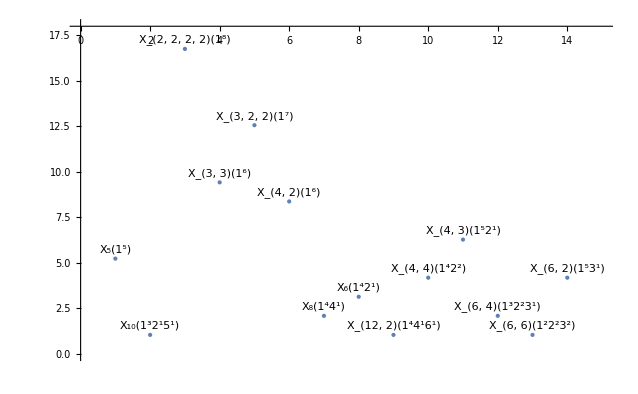

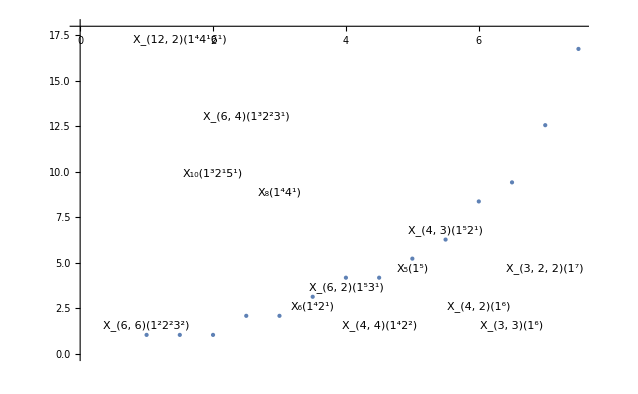

```mathematica
data = {5.235987755982989, 1.0471975511965976,16.755160819145562,9.42477796076938,12.566370614359172, 8.377580409572781, 2.0943951023931953, 3.141592653589793, 1.0471975511965976,4.1887902047863905, 6.283185307179586, 2.0943951023931953, 1.0471975511965976, 4.1887902047863905,-1};
dataORD = Sort[data]
elements = {"CY1", "CY2", "CY3", "CY4", "CY5", "CY6", "CY7", "CY8", "CY9", "CY10", "CY11",
   "CY12", "CY13", "CY14"};
elementsX = {"X_5(1^5)", "X_10(1^32^15^1)", "X_(2, 2, 2, 2)(1^8)", "X_(3, 3)(1^6)", "X_(3, 2, 2)(1^7)", "X_(4, 2)(1^6)", "X_8(1^44^1)", "X_6(1^42^1)", "X_(12, 2)(1^44^16^1)", "X_(4, 4)(1^42^2)", "X_(4, 3)(1^52^1)",
   "X_(6, 4)(1^32^23^1)", "X_(6, 6)(1^22^23^2)", "X_(6, 2)(1^53^1)",""};

elementsXORD = {"","X_(6, 6)(1^22^23^2)","X_(12, 2)(1^44^16^1)","X_10(1^32^15^1)","X_(6, 4)(1^32^23^1)","X_8(1^44^1)","X_6(1^42^1)","X_(6, 2)(1^53^1)","X_(4, 4)(1^42^2)","X_5(1^5)","X_(4, 3)(1^52^1)","X_(4, 2)(1^6)","X_(3, 3)(1^6)","X_(3, 2, 2)(1^7)","X_(2, 2, 2, 2)(1^8)"}

dataPlot = ListPlot[data, PlotStyle -> PointSize -> Large,PlotStyle->Red, AxesOrigin -> {0, 18},Axes->{None,True} ,PlotRange -> {Automatic, {0, 18}}];
labels = MapThread[Text[#1, {#2, #3 + 0.5}] &, {elementsX, Range[Length@data], data}];
Show[dataPlot, Graphics[labels]]

dataPlot = ListPlot[dataORD, PlotStyle -> PointSize -> Large,PlotStyle->Red,Ticks -> {Charting`FindTicks[{0, 2}, {0, 1}], Automatic}, AxesOrigin -> {0, 18},Axes->{None,True} ,PlotRange -> {Automatic, {0, 18}}];
labels = MapThread[Text[#1, {#2, #3 + 0.5}] &, {elementsXORD, Range[Length@data], data}];
Show[dataPlot, Graphics[labels]]
```

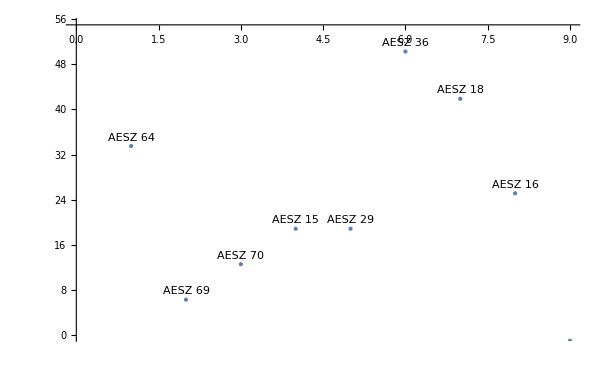

```mathematica
data2= {33.510321638291124, 6.283185307179586,12.566370614359172, 18.84955592153876 ,18.84955592153876 , 5 25.132741228718345 , 41.88790204786391,0.26548245743669 ,-1};

elementsX2 = { "AESZ 64", "AESZ 69", "AESZ 70", "AESZ 15", "AESZ 29","AESZ 36", "AESZ 18","AESZ 16" ,""};

dataPlot2 = ListPlot[data2, PlotStyle -> PointSize -> Large,PlotStyle->Red, AxesOrigin -> {0, 55},Axes->{None,True} ,PlotRange -> {Automatic, {0, 55}}];
labels2 = MapThread[Text[#1, {#2, #3 + 1.5}] &, {elementsX2, Range[Length@data2], data2}];
Show[dataPlot2, Graphics[labels2]]
```

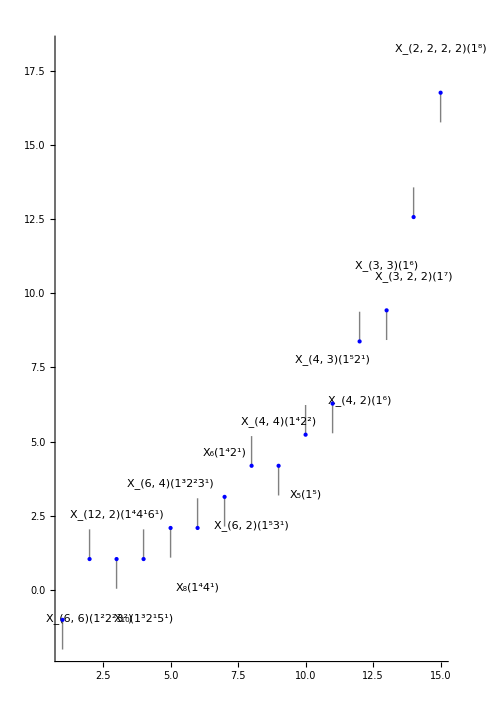

```mathematica
With[{coord=MapIndexed[{#2[[1]],#1}&,dataORD]},Graphics[{MapThread[Style[Text[#1,#2+If[OddQ[#2[[1]]],{0,1.5},{0,-2}]],Black,12,Italic]&,{elementsXORD,coord}],PointSize[Large],Gray,Line[{#,#+If[OddQ[#[[1]]],{0,-1},{0,1}]}]&/@coord,Blue,Point@coord},Axes->{None,True},AspectRatio->Automatic,AxesOrigin->{0,9},ImageSize->500]]
```

# Orden 2

```mathematica
36;
PF[z_, F_] := 
  (z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) & [F]]]] - 
   2^4 z ((2 z D[#, z] + 1)^2 &[
      (3 (z D[#, z])^2 + 3 z D[#, z] + 1) &[F]]) + 
   2^9 z^2 ((2 z D[#, z] + 1)^2 &[
      (2 z D[#, z] + 3)^2 &[F]])
χ = -88; c2D = 80; k = 32;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

33.5103 n^2 y^3-10.472 n^2 y+0.669866 n^2+(0.818123 n^2)/y+O[1/y]^2

33.5103 n^2 y^3-10.472 n^2 y+0.669866 n^2+\frac{0.818123
   n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
64;
PF[z_, F_] := 
  (z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) & [F]]]] - 
   2^2 3 z ((6 z D[#, z] + 1) &[(6 z D[#, z] + 5) &[
      (10 (z D[#, z])^2 + 10 z D[#, z] + 3) &[F]]]) + 
   2^4 3^4 z^2 ((6 z D[#, z] + 1) &[(6 z D[#, z] + 5) &[
      (6 z D[#, z] + 7) &[(6 z D[#, z] + 11) &[F]]]])
χ = -364; c2D = 72; k = 6;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

6.28319 n^2 y^3-9.42478 n^2 y+2.77081 n^2+(3.53429 n^2)/y+O[1/y]^2

6.28319 n^2 y^3-9.42478 n^2 y+2.77081 n^2+\frac{3.53429 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
69;
PF[z_, F_] := 
  (z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) & [F]]]] - 
   2^2 z (4 z D[#, z] + 1) &[(4 z D[#, z] + 3) &[(10 (z D[#, z])^2 + 10 z D[#, z] + 3) &[F]]] + 2^4 3^2 z^2 ((4 z D[#, z] + 1) &[(4 z D[#, z] + 3) &[(4 z D[#, z] + 5) &[(4 z D[#, z] + 7) &[F]]]])
χ = -224; c2D = 72; k = 12;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

12.5664 n^2 y^3-9.42478 n^2 y+1.70511 n^2+(1.76715 n^2)/y+O[1/y]^2

12.5664 n^2 y^3-9.42478 n^2 y+1.70511 n^2+\frac{1.76715 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
70;
PF[z_, F_] := 
  (z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) &[z D[#, z] & [F]]]] - 
   z 3 ((3 z D[#, z] + 1 #) &[(3 z D[#, z] + 2 #) &[(10 (z D[z D[#, z], z]) + 10 z D[#, z] + 3 #) &[F]]]) + 
   3^4 z^2 ((3 z D[#, z] + 1 #) &[(3 z D[#, z] + 2 #) &[
      (3 z D[#, z] + 4 #) &[(3 z D[#, z] + 5 #) &[F]]]])
χ = -156; c2D = 72; k = 18;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

18.8496 n^2 y^3-9.42478 n^2 y+1.18749 n^2+(1.1781 n^2)/y+O[1/y]^2

18.8496 n^2 y^3-9.42478 n^2 y+1.18749 n^2+\frac{1.1781 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
15;
PF[z_,F_]:= 
	(z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) &[z D[#, z] & [F]]]] - 
   z 3 ((3 z D[#, z] + 1 #) &[(3 z D[#, z] + 2 #) &[(7(z D[z D[#, z], z]) + 7 z D[#, z] + 2 #) &[F]]]) - 
   2^3 3^2 z^2 ((3 z D[#, z] + 1 #) &[(3 z D[#, z] + 2 #) &[
      (3 z D[#, z] + 4 #) &[(3 z D[#, z] + 5 #) &[F]]]])
χ = -162; c2D = 72; k = 18;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

18.8496 n^2 y^3-9.42478 n^2 y+1.23316 n^2+(1.1781 n^2)/y+O[1/y]^2

18.8496 n^2 y^3-9.42478 n^2 y+1.23316 n^2+\frac{1.1781
   n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
16;
PF[z_,F_]:= 
	(z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) &[z D[#, z] & [F]]]] - 
   z 2^2 ((2 z D[#, z] + 1 #) &[(2 z D[#, z] + 1 #) &[(5(z D[z D[#, z], z]) + 5 z D[#, z] + 2 #) &[F]]]) + 
   2^8 z^2 ((2 z D[#, z] + 1 #) &[( z D[#, z] + 1 #) &[
      ( z D[#, z] + 4 #) &[(2 z D[#, z] + 3 #) &[F]]]])
χ = -128; c2D = 96; k = 48;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

50.2655 n^2 y^3-12.5664 n^2 y+0.974351 n^2+(0.785398 n^2)/y+O[1/y]^2

50.2655 n^2 y^3-12.5664 n^2 y+0.974351 n^2+\frac{0.785398
   n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
17;
PF[z_,F_]:= 5^2 (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]] - 15z(51z D[#,z]&[(z D[#,z])&[(z D[#,z])&[(z D[#,z])]]] +84z D[#,z]&[(z D[#,z])&[(z D[#,z])]] + 72z D[#,z]&[(z D[#,z])] +30z D[#,z] +5)&[F] + 6 z^2(531z D[#,z]&[(z D[#,z])&[(z D[#,z])&[(z D[#,z])]]] +828z D[#,z]&[(z D[#,z])&[(z D[#,z])]] + 541z D[#,z]&[(z D[#,z])] +155z D[#,z] +15)&[F] -54 z^3 (423z D[#,z]&[(z D[#,z])&[(z D[#,z])&[(z D[#,z])]]] +2160z D[#,z]&[(z D[#,z])&[(z D[#,z])]] + 4399z D[#,z]&[(z D[#,z])] +3795z D[#,z] +1170)&[F]+ 3^5 z^4(279z D[#,z]&[(z D[#,z])&[(z D[#,z])&[(z D[#,z])]]] +1368z D[#,z]&[(z D[#,z])&[(z D[#,z])]] + 2270z D[#,z]&[(z D[#,z])] +1586z D[#,z] +402)&[F]- 3^(10) z^5 (z D[#,z]+1 #)&[(z D[#,z]+1#)&[( z D[#,z]+1 #)&[(z D[#,z]+1#)&[F]]]]
χ = ; c2D = ; k = ;
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
18;
PF[z_,F_]:= 
	(z D[#, z]) &[(z D[#, z]) &[(z D[#, z]) &[z D[#, z] & [F]]]] - 
   z 2^2 ((2 z D[#, z] + 1 #) &[(2 z D[#, z] + 1 #) &[(3(z D[z D[#, z], z]) + 3 z D[#, z] + 1 #) &[F]]]) - 
   2^4 z^2 ((2 z D[#, z] + 1 #) &[( 4z D[#, z] + 3 #) &[
      ( 4 z D[#, z] + 5 #) &[(2 z D[#, z] + 3 #) &[F]]]])
χ = -128; c2D = 88; k =40;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

41.8879 n^2 y^3-11.5192 n^2 y+0.974351 n^2+(0.791943 n^2)/y+O[1/y]^2

41.8879 n^2 y^3-11.5192 n^2 y+0.974351 n^2+\frac{0.791943
   n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
19;
PF[z_,F_]:= 23^2 (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]] - 23z(921z D[#,z]&[(z D[#,z])&[(z D[#,z])&[(z D[#,z])]]] +2046z D[#,z]&[(z D[#,z])&[(z D[#,z])]] + 1644z D[#,z]&[(z D[#,z])] +621z D[#,z] +92)&[F] - z^2(380851z D[#,z]&[(z D[#,z])&[(z D[#,z])&[(z D[#,z])]]] +1328584z D[#,z]&[(z D[#,z])&[(z D[#,z])]] + 1772673z D[#,z]&[(z D[#,z])] +1033528z D[#,z] +221168)&[F] -2 z^3 (475861z D[#,z]&[(z D[#,z])&[(z D[#,z])&[(z D[#,z])]]] +1310172z D[#,z]&[(z D[#,z])&[(z D[#,z])]] + 1028791z D[#,z]&[(z D[#,z])] +208932z D[#,z] -27232)&[F]+ 2^2 17 z^4(8873z D[#,z]&[(z D[#,z])&[(z D[#,z])&[(z D[#,z])]]] +14020z D[#,z]&[(z D[#,z])&[(z D[#,z])]] + 5139z D[#,z]&[(z D[#,z])] -1664z D[#,z] -976)&[F]+2^3 3 17^2 z^5 (z D[#,z]+1 #)&[(z D[#,z]+1#)&[(3z D[#,z]+2 #)&[(3z D[#,z]+4#)&[F]]]]
χ = ; c2D = ; k = ;
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
PF[z_,F_]:= 7^2 (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]] - 7 z ()
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
24,
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 3(3z D[#,z]+1 #)&[(3z D[#,z]+2#)&[(11[z D[z D[#,z],z]]+11z D[#,z]+3#)&[F]]]-3^2z^2(3z D[#,z]+1 #)&[(3 z D[#,z]+2#)&[(3 z D[#,z]+4#)&[(3z D[#,z]+5#)&[F]]]]
c2D = ; k = ; χ = ;
χ = ; c2D = ; k = ;
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
25;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^2(2z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(11[z D[z D[#,z],z]]+11z D[#,z]+3#)&[F]]]-2^4z^2(2z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(2z D[#,z]+3#)&[(2z D[#,z]+3#)&[F]]]]
χ = ; c2D = ; k = ;
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
26,
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2(2z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(13[z D[z D[#,z],z]]+13z D[#,z]+4#)&[F]]]-2^3 3z^2(2z D[#,z]+1 #)&[(3z D[#,z]+2#)&[(3z D[#,z]+4#)&[(2z D[#,z]+3#)&[F]]]]
χ = ; c2D = ; k = ;
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------------------*)
29;
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2(2z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(17 z D[#,z]&[(z D[#,z])] +17z D[#,z]+5#)&[F]]]-2^2z^2(2z D[#,z]+1 #)&[(z D[#,z]+1#)&[(z D[#,z]+1#)&[(2z D[#,z]+3#)&[F]]]]
c2D =72 ; k = 24; χ =-116 ;
```

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

25.1327 n^2 y^3-9.42478 n^2 y+0.883005 n^2+(0.883573 n^2)/y+O[1/y]^2

25.1327 n^2 y^3-9.42478 n^2 y+0.883005 n^2+\frac{0.883573
   n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
Sort[{{1,5.23599},{1,1.0472},{1,16.755160819145562},{1,9.42478},{1,12.5664},{1,8.37758},{1,2.0944},{1,3.1415}}]
```

{{1,1.0472},{1,2.0944},{1,3.1415},{1,5.23599},{1,8.37758},{1,9.42478},{1,12.5664},{1,16.7552}}

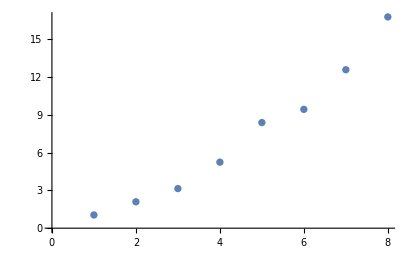

```mathematica
ListPlot[{{1,1.0472},{2,2.0944},{3,3.1415},{4,5.23599},{5,8.37758},{6,9.42478},{7,12.5664},{8,16.755160819145562}}]
```

## Period LCS

```mathematica
(*PRIMER PERIODO*)
Num = 2; 
sample =1;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]
c2D = 50; k = 5; χ = -200;
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
Print["1st Period Π_1(...)= ",wM0]
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
Print["2st Period Π_2(...)= ",wM1];
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
Print["3dt Period Π_3(...)= ", wM2] 
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
Print["4ht Period Π_4(...)=  ",wM3]
(**)
Print["--------------------------------------------------------------------------------"]
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};
sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)
Print["--------------------------------------------------------------------------------"]
(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]
Print["--------------------------------------------------------------------------------"]
(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt]


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};
Print["Period Vector Log[z]-> 2 π i t, and then t -> x + i y"]
MatrixForm[ΠSt]
MatrixForm[ΠStxy]
Print["--------------------------------------------------------------------------------"];
ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;
Print["Conjugate Period Vector t -> x - i y"]
MatrixForm[ΠStxyC]
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]]
Print["--------------------------------------------------------------------------------"];
Print["Charges"]
q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0}
Print["Vafa Order: ",MatrixForm[QU],", x->0: ",MatrixForm[Q],", Series y->Infty: ",MatrixForm[Cargas],", Polar: ", MatrixForm[QU/.{x->1/(2 Pi I)Log[r], y->1/(2 Pi I) p}]]
Print["--------------------------------------------------------------------------------"]
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify
Print["Kahler Potential:"]
Print["K = ",Series[k,{y,Infinity,3}]]
(* metrica de Kahler*)
Print["--------------------------------------------------------------------------------"]
Print["Metrica de Kahler:"]
G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
Print["g_(t,tc)= ∂_t ∂_tc K = ", G[1,1]//Simplify]
Print["Metrica de Kahler leading terms:"]
Print["g_(t,tc)= ∂_t ∂_tc K = ", Series[G[1,1],{t,Infinity,2},{tc,Infinity,2}]]
Print["--------------------------------------------------------------------------------"]
Print["Metrica de Kahler:"]
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
Print["g_(t,tc)= ∂_t ∂_tc K = ",g]
Print["--------------------------------------------------------------------------------"]
Print["Metrica de Kahler a leading terms: "];
glead = Series[g,{y,Infinity,3}]//Simplify;
Print["g_(t,tc)= ∂_t ∂_tc K = ",glead//Expand]
Print["--------------------------------------------------------------------------------"]
Print["Distancia en el Moduli space:"]
distance = Integrate[Sqrt[glead/.x->0],y];
Print["d = ∫√(g_(z,zc))ⅆz = ", distance]
Sol = Solve[distance==d, y]
Print["----------------------------------------------------------------"]
Print["Carga Central Z"]
Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Print["Z = ", Z ]
Print["----------------------------------------------------------------"]
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
Print["Entropy / Central Charge:"] 
Print["S = π |Z|^2 =", Sent]
Print["----------------------------------------------------------------"]
S = Series[Sent,{y,Infinity,1}] //Simplify;
Print["Entropy / Central Charge leading terms:"]
Print[" S = π |Z|^2 =", S/.{x->0}]
TeXForm[ S/.{x->0}]
```

1st Period Π_1(...)= 1+120 z+113400 z^2

2st Period Π_2(...)= 770 z+810225 z^2+(4418351000 z^3)/3+Log[z]+120 z Log[z]+113400 z^2 Log[z]

3dt Period Π_3(...)= 575 z+(4208175 z^2)/4+(15282842000 z^3)/9+770 z Log[z]+810225 z^2 Log[z]+4418351000/3 z^3 Log[z]+Log[z]^2/2+60 z Log[z]^2+56700 z^2 Log[z]^2

4ht Period Π_4(...)=  -1150 z-(3298375 z^2)/4-(39934899875 z^3)/54+575 z Log[z]+4208175/4 z^2 Log[z]+15282842000/9 z^3 Log[z]+385 z Log[z]^2+810225/2 z^2 Log[z]^2+2209175500/3 z^3 Log[z]^2+Log[z]^3/6+20 z Log[z]^3+18900 z^2 Log[z]^3

--------------------------------------------------------------------------------

--------------------------------------------------------------------------------

Periodos en base Simpléctica:

ΠS=((0.-0.969204 ⅈ)-(25 ⅈ Log[z])/(24 π)+(5 ⅈ Log[z]^3)/(48 π^3)
25/12+(ⅈ Log[z])/(4 π)+(5 Log[z]^2)/(8 π^2)
1
-(ⅈ Log[z])/(2 π))

--------------------------------------------------------------------------------

((0.-0.969204 ⅈ)+(25 t)/12+(5 t^3)/6
25/12-t/2-(5 t^2)/2
1
t)

Period Vector Log[z]-> 2 π i t, and then t -> x + i y

((0.-0.969204 ⅈ)+(25 t)/12+(5 t^3)/6
25/12-t/2-(5 t^2)/2
1
t)

((0.-0.969204 ⅈ)+25/12 (x+ⅈ y)+5/6 (x+ⅈ y)^3
25/12+1/2 (-x-ⅈ y)-5/2 (x+ⅈ y)^2
1
x+ⅈ y)

--------------------------------------------------------------------------------

Conjugate Period Vector t -> x - i y

(0.+(25 x)/12+(5 x^3)/6-(5 x y^2)/2+ⅈ (0.969204-(25 y)/12-(5 x^2 y)/2+(5 y^3)/6)
25/12-x/2-(5 x^2)/2+(5 y^2)/2+ⅈ (y/2+5 x y)
1
x-ⅈ y)

((0.+0.969204 ⅈ)+(25 tc)/12+(5 tc^3)/6
25/12-tc/2-(5 tc^2)/2
1
tc)

--------------------------------------------------------------------------------

Charges

{0,n,-n y^2,0}

Vafa Order: (-5/2 n x y^2
(5 n y^2)/2
n
n x), x->0: (0
1/2 n (25/6+5 y^2)
n
0), Series y->Infty: (-5/2 (n x) y^2+O[1/y]^3
(5 n y^2)/2+1/2 n (25/6-x-5 x^2)+O[1/y]^3
n
n x), Polar: (-(5 ⅈ n p^2 Log[r])/(16 π^3)
-(5 n p^2)/(8 π^2)
n
-(ⅈ n Log[r])/(2 π))

--------------------------------------------------------------------------------

-1. (1.89712+Log[0.290761+1. y^3])

Kahler Potential:

K = -1. (1.89712+1. Log[1. y^3])-0.290761/y^3+O[1/y]^4

--------------------------------------------------------------------------------

Metrica de Kahler:

g_(t,tc)= ∂_t ∂_tc K = -(6. (t^4-(0.+4.65218 ⅈ) tc-4. t^3 tc+6. t^2 tc^2+tc^4+t ((0.+4.65218 ⅈ)-4. tc^3)))/(((0.-2.32609 ⅈ)+t^3-3. t^2 tc+3. t tc^2-1. tc^3)^2)

Metrica de Kahler leading terms:

g_(t,tc)= ∂_t ∂_tc K = -6/t^2+O[1/t]^3

--------------------------------------------------------------------------------

Metrica de Kahler:

g_(t,tc)= ∂_t ∂_tc K = (1.5 ((-0.581523+0. ⅈ) y+y^4))/(((0.290761+0. ⅈ)+y^3)^2)

--------------------------------------------------------------------------------

Metrica de Kahler a leading terms:

g_(t,tc)= ∂_t ∂_tc K = 1.5/y^2+O[1/y]^4

--------------------------------------------------------------------------------

Distancia en el Moduli space:

d = ∫√(g_(z,zc))ⅆz = 1.22474 Log[y]+O[1/y]^2

{{y→1. ⅇ^(0.816497 d)}}

----------------------------------------------------------------

Carga Central Z

Z = 1/(√(0.290761+y^3))0.387298 n ((0.+0.969204 ⅈ)+1.66667 x^3+x (-4.16667+(0.+0.5 ⅈ) y)+x^2 (0.5+(0.+2.5 ⅈ) y)-(0.+2.08333 ⅈ) y+(0.+3.33333 ⅈ) y^3)

----------------------------------------------------------------

Entropy / Central Charge:

S = π |Z|^2 =1/((0.290761+0. ⅈ)+y^3)(0.471239+0. ⅈ) n^2 ((0.-0.969204 ⅈ)+1.66667 x^3+x (-4.16667-(0.+0.5 ⅈ) y)+x^2 (0.5-(0.+2.5 ⅈ) y)+(0.+2.08333 ⅈ) y-(0.+3.33333 ⅈ) y^3) ((0.+0.969204 ⅈ)+1.66667 x^3+x (-4.16667+(0.+0.5 ⅈ) y)+x^2 (0.5+(0.+2.5 ⅈ) y)-(0.+2.08333 ⅈ) y+(0.+3.33333 ⅈ) y^3)

----------------------------------------------------------------

Entropy / Central Charge leading terms:

S = π |Z|^2 =5.23599 n^2 y^3-6.54498 n^2 y+1.52242 n^2+(2.04531 n^2)/y+O[1/y]^2

5.23599 n^2 y^3-6.54498 n^2 y+1.52242 n^2+\frac{2.04531 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
Clear[n]
SMQ = 28.797932657906454 n^2 y^3 ;
S1 = 5.759586531581287 n^2 y^3 ;
S2 = 92.15338450530062 n^2 y^3;
S3 = 51.836278784231595 n^2 y^3;
S4 = 138.2300767579509 n^2 y^3;
```

```mathematica
SMQp= 28.797932657906454 n^2 y^3 /.{y->1. ⅇ^(0.5909368402852788 d)};
S1p = 5.759586531581287 n^2 y^3/.{y->1. ⅇ^(0.5909368402852788 d)};
S2p = 92.15338450530062 n^2 y^3/.{y->1. ⅇ^(0.5909368402852788 d)};
S3p = 51.836278784231595 n^2 y^3/.{y->1. ⅇ^(0.5909368402852788 d)};
S4p = 138.2300767579509 n^2 y^3/.{y->1. ⅇ^(0.5909368402852788 d)};
```

-Graphics3D-

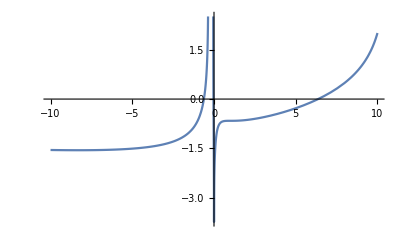

```mathematica
Kal = -Log[ - I ΠSc[zc].Σ.ΠS[z]]/.{z->a+ I b, zc-> a-I b};
Plot3D[Kal,{a,b}∈Disk[{0,0},0.5],ClippingStyle->None,PlotRange->{Automatic,Automatic,{-3,3}}]
Plot[-Log[ - I ΠSc[zc].Σ.ΠS[z]]/.{zc->0},{z,-10,10}]
```

```mathematica
Plot3D[g,{x,y}∈Disk[{0,0},2]]
```

-Graphics3D-

```mathematica
Plot3D[k,{y,-1,1},{x,-1,1},PlotRange->{All,All,{-5,5}},PlotTheme->"ThickSurface"]
```

-Graphics3D-

```mathematica
g
```

(0.5 (x^4-(0.0930436+0. ⅈ) y+2. x^2 y^2+3.08 y^4))/(((-0.0387682+0. ⅈ)+x^2 y-0.733333 y^3)^2)

```mathematica
Plot3D[g,{y,0,1},{x,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[{SMQ,S1,S2,S3},{n,0,1000},{y,0,1000},ColorFunction->"SunsetColors",PlotRange->All]
```

-Graphics3D-

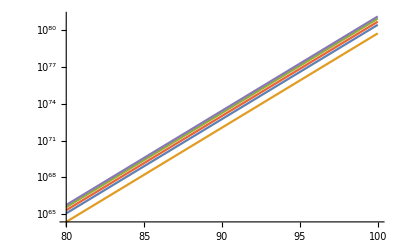

```mathematica
LogPlot[{SMQp/.{n->10},S1p/.{n->10},S2p/.{n->10},S3p/.{n->10},S4p/.{n->10}},{d,80,100}]
```

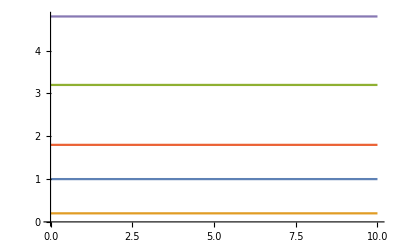

```mathematica
Plot[{SMQp/SMQp /.{n->10},S1p/SMQp /.{n->10},S2p/SMQp /.{n->10},S3p/SMQp /.{n->100},S4p/ SMQp/.{n->10}},{y,0,10}]
```

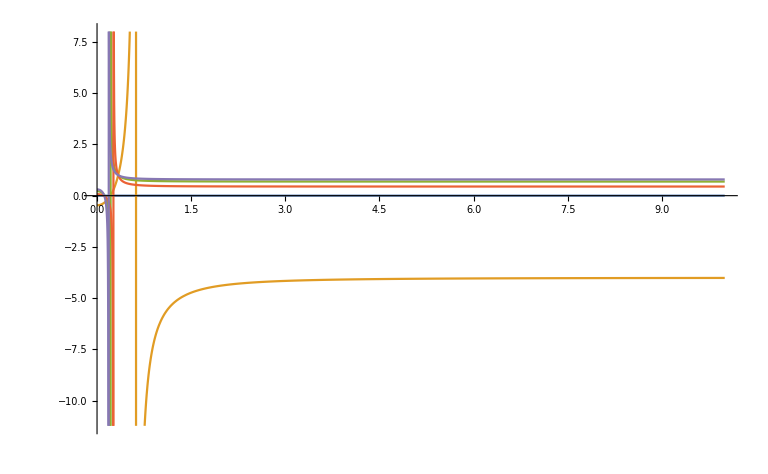

```mathematica
Plot[{1-SMQ/SMQ /.{n->10},1-SMQ/S1 /.{n->10},1-SMQ/S2 /.{n->10},1-SMQ/S3 /.{n->100},1-SMQ/S4 /.{n->100}},{y,0,10}]
```

```mathematica
s=Normal[Sent]
```

-(((0.0628319+0. ⅈ) n^2 ((0.-0.969204 ⅈ)-10.8333 x^3+(0.+32.5 ⅈ) x^2 y+40. x y^2-(0.+18.3333 ⅈ) y^3) ((0.+0.969204 ⅈ)-3.33333 x^3+x (-4.16667-(0.+0.5 ⅈ) y)+x^2 (-0.5-(0.+17.5 ⅈ) y)-(0.+2.08333 ⅈ) y+(0.+18.3333 ⅈ) y^3))/((-0.0387682+0. ⅈ)+x^2 y-0.733333 y^3))

```mathematica
Re[Normal[S]]/.{x->0,n->10}
```

152.242+Re[-327.249 y+2879.79 y^3]

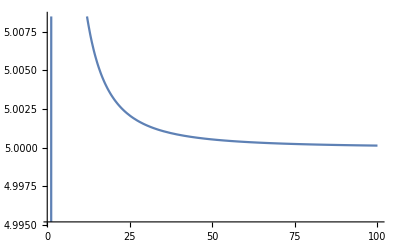

```mathematica
Plot[s/(5.759586531581287 n^2 y^3+(0.+12.566370614359172 ⅈ) n^2 x y^2-7.853981633974483 (n^2 (0.2833333333333333+0.1 x+1. x^2)) y+(0.+2.784593488409136 ⅈ) n^2 ((0.-0.787292262705387 ⅈ)-0.14529914529914556 x-0.33333333333333326 x^2+1. x^3)-1/y 3.2486924031439903 (n^2 x ((0.+1.717795624914528*^-16 ⅈ)+2.708791208791209 x+0.4285714285714286 x^2+1. x^3)))/.{x->0,n->10}/.{x->0,n->10},{y,1,100}]
```

```mathematica
ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
ΠStxy = ΠSt/.{t->x+I y};
Print["Period Vector Log[z]-> 2 π i t, and then t -> x + i y"]
MatrixForm[ΠSt]
MatrixForm[ΠStxy]
Print["--------------------------------------------------------------------------------"]
ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;
Print["Conjugate Period Vector t -> x - i y"]
MatrixForm[ΠStxyC]

sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}]
ΠStC[tc];
MatrixForm[ΠStC[tc]]
Print["--------------------------------------------------------------------------------"]
p0 = (n (2 Pi I /5)^(-3) ΠStxy[[1]] +  n ( -2 Pi I/5)^(-3) ΠStxyC[[1]]) // Simplify ;
p1 = (n (2 Pi I /5)^(-3) ΠStxy[[2]] +  n ( -2 Pi I /5)^(-3) ΠStxyC[[2]]) //Simplify ;
q0 = (n (2 Pi I /5)^(-3) ΠStxy[[3]] +  n ( -2 Pi I /5)^(-3) ΠStxyC[[3]]) //Simplify ; 
q1 = (n (2 Pi I /5)^(-3) ΠStxy[[4]] +  n ( -2 Pi I /5)^(-3) ΠStxyC[[4]]) //Simplify ;
QU={p0,p1,q0,q1}
Print["--------------------------------------------------------------------------------"]

K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
(* metrica de Kahler*)
Print["Metrica de Kahler"]
G[1,1]=D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
Print["g_(t,tc)= ", G[1,1]//Simplify]
Print["Metrica de Kahler leading terms "]
Print["g_(t,tc)= ", leadingSeries[G[1,1],t,tc]//Simplify]
Print["Check"]
G[1,1]/.{t->0.00000001,tc->0.00000001}//Simplify 
leadingSeries[G[1,1],t,tc]/.{t->0.00000001,tc->0.00000001}//Simplify 
Print["--------------------------------------------------------------------------------"]
Print["Metrica de Kahler"]
g = G[1,1]/.{t-> x+I y, tc-> x- I y}//Simplify;
Print["g_(t,tc)= ",g]
Print["Metrica de Kahler leading terms"]
glead = leadingSeries[G[1,1],t,tc]/.{t-> x+I y, tc-> x- I y}//Simplify;
Print["g_(t,tc)= ",glead//Expand]
Print["--------------------------------------------------------------------------------"]
distance = Integrate[Sqrt[glead/.x->0],y];
Print["d = ∫√(g_(z,zc))ⅆz = ", distance]

(*K[z_,zc_]:=-Log[-I ΠSc[zc].Σ.ΠS[z]];
Print["--------------------------------------------------------------------------------"]
Print["Métrica de Kahler"]
G[1,1]=D[K[z,zc],z,zc];
metric=leadingSeries[G[1,1]/.zc->-z//Simplify,z,zc];
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;
Print["g_(z,zc)= ", metric]
Print["--------------------------------------------------------------------------------"]
d = Integrate[leadingSeries[Sqrt[gzzc],z,zc],z]//Expand;
Print["d = ∫√(g_(z,zc))ⅆz = ", d]
Print["--------------------------------------------------------------------------------"]
Print["t = ", T = leadingSeries[Series[1/(2 Pi I)wM1/wM0,{z,0,3}],z,zc] ]
Print["--------------------------------------------------------------------------------"]
Plot[d,{z,0,10}]*)
```

Period Vector Log[z]-> 2 π i t, and then t -> x + i y

((0.-1.39565 ⅈ)+(17 t)/12+(13 t^3)/6
17/12+t/2-(3 t^2)/2
1
t)

((0.-1.39565 ⅈ)+17/12 (x+ⅈ y)+13/6 (x+ⅈ y)^3
17/12+1/2 (x+ⅈ y)-3/2 (x+ⅈ y)^2
1
x+ⅈ y)

--------------------------------------------------------------------------------

Conjugate Period Vector t -> x - i y

(0.+(17 x)/12+(13 x^3)/6-(13 x y^2)/2+ⅈ (1.39565-(17 y)/12-(13 x^2 y)/2+(13 y^3)/6)
17/12+x/2-(3 x^2)/2+(3 y^2)/2+ⅈ (-y/2+3 x y)
1
x-ⅈ y)

((0.+1.39565 ⅈ)+(17 tc)/12+(13 tc^3)/6
17/12+tc/2-(3 tc^2)/2
1
tc)

--------------------------------------------------------------------------------

{n ((1.40662+0. ⅈ)+((-1.4278+0. ⅈ)-(6.55109+0. ⅈ) x^2) y+(2.1837+0. ⅈ) y^3),(125 n (-1+6 x) y)/(8 π^3),0,-(125 n y)/(4 π^3)}

--------------------------------------------------------------------------------

Metrica de Kahler

g_(t,tc)= -((0.692308 (t^4-(0.+2.57659 ⅈ) tc-4. t^3 tc+13.6923 t^2 tc^2+tc^4+t ((0.+2.57659 ⅈ)-4. tc^3)))/((0.-1.2883 ⅈ)+t^3-0.692308 t^2 tc+0.692308 t tc^2-1. tc^3)^2)

Metrica de Kahler leading terms

g_(t,tc)= (0.-1.07476 ⅈ) tc

Check

3.20866×10^-32+0. ⅈ

0.-1.07476×10^-8 ⅈ

--------------------------------------------------------------------------------

Metrica de Kahler

g_(t,tc)= (0.25 (x^4-(0.669914+0. ⅈ) y+2. x^2 y^2+3.08 y^4))/(((-0.279131+0. ⅈ)+x^2 y-0.733333 y^3)^2)

Metrica de Kahler leading terms

g_(t,tc)= (0.-1.07476 ⅈ) x-(1.07476+0. ⅈ) y

--------------------------------------------------------------------------------

d = ∫√(g_(z,zc))ⅆz = 0.691139 √-y y

```mathematica
q={p0,p1,q0,q1}
Z = q.Σ.ΠS[z]/(Sqrt[-I ΠSc[zc].Σ.ΠS[z]])//Simplify
Zc = (p0 π^3+(0.-30.05142257898986 ⅈ) q0-64.59640975062462 q1+((0.+4.934802200544679 ⅈ) p1+(0.-10.280837917801419 ⅈ) q0-(0.-27.141412102995734 ⅈ) q1) Log[zc]-5.890486225480862 q1 Log[zc]^2-(0.-2.760416666666667 ⅈ) q0 Log[zc]^3)/(π^3 √(1.9384089801458408-0.08902767317497778 Log[zc]^3-0.03023581353112453 Log[zc]^2 Log[z]-0.03023581353112453 Log[zc] Log[z]^2-0.08902767317497778 Log[z]^3))
Z2 = Z Zc //Simplify
```

{p0,p1,q0,q1}

(p0 π^3+(0.+30.0514 ⅈ) q0-64.5964 q1+((0.-4.9348 ⅈ) p1+(0.+10.2808 ⅈ) q0-(0.+27.1414 ⅈ) q1) Log[z]-5.89049 q1 Log[z]^2-(0.+2.76042 ⅈ) q0 Log[z]^3)/(π^3 √(1.93841-0.0890277 Log[z]^3-0.0302358 Log[z]^2 Log[zc]-0.0302358 Log[z] Log[zc]^2-0.0890277 Log[zc]^3))

(p0 π^3-(0.+30.0514 ⅈ) q0-64.5964 q1+((0.+4.9348 ⅈ) p1-(0.+10.2808 ⅈ) q0+(0.+27.1414 ⅈ) q1) Log[zc]-5.89049 q1 Log[zc]^2+(0.+2.76042 ⅈ) q0 Log[zc]^3)/(π^3 √(1.93841-0.0890277 Log[z]^3-0.0302358 Log[z]^2 Log[zc]-0.0302358 Log[z] Log[zc]^2-0.0890277 Log[zc]^3))

-((11.2325 (1. p0+(0.+0.969204 ⅈ) q0-2.08333 q1+((0.-0.159155 ⅈ) p1+(0.+0.331573 ⅈ) q0-(0.+0.875352 ⅈ) q1) Log[z]-0.189977 q1 Log[z]^2-(0.+0.0890277 ⅈ) q0 Log[z]^3) (1. p0-(0.+0.969204 ⅈ) q0-2.08333 q1+((0.+0.159155 ⅈ) p1-(0.+0.331573 ⅈ) q0+(0.+0.875352 ⅈ) q1) Log[zc]-0.189977 q1 Log[zc]^2+(0.+0.0890277 ⅈ) q0 Log[zc]^3))/(-21.7731+1. Log[z]^3+0.339623 Log[z]^2 Log[zc]+0.339623 Log[z] Log[zc]^2+1. Log[zc]^3))

```mathematica
q={p0,p1,q0,q1};
Zet=leadingSeries[Sqrt[(q.Σ.ΠS[z])(q.Σ.ΠSc[zc])]/Sqrt[-I ΠSc[zc].Σ.ΠS[z]],z,zc]
K[t_,tc_,z_,zc_]:=-Log[-I ΠSc[zc].Σ.ΠS[z]];
(* metrica de Kahler*)
G[1,1]=D[K[t,tc,z,zc],z,zc];

ecu = 1/G[1,1](D[Log[Zet],zc]D[U[z,zc],z]+D[Log[Zet],z]D[U[z,zc],zc])==1;
DSolve[ecu, U[z,zc],z,zc]
```

(0.191586 √((p0 π^2+(0.+9.56566 ⅈ) q0-20.5617 q1-(0.+1.5708 ⅈ) p1 Log[z]+(0.+3.27249 ⅈ) q0 Log[z]-(0.+8.63938 ⅈ) q1 Log[z]-1.875 q1 Log[z]^2-(0.+0.878668 ⅈ) q0 Log[z]^3) (p0 π^3-(0.+30.0514 ⅈ) q0-64.5964 q1+(0.+4.9348 ⅈ) p1 Log[zc]-(0.+10.2808 ⅈ) q0 Log[zc]+(0.+27.1414 ⅈ) q1 Log[zc]-5.89049 q1 Log[zc]^2+(0.+2.76042 ⅈ) q0 Log[zc]^3)))/(√(21.7731+1.5878×10^-15 Log[z]-1. Log[z]^3+1.5878×10^-15 Log[zc]-0.339623 Log[z]^2 Log[zc]-0.339623 Log[z] Log[zc]^2-1. Log[zc]^3))

$Aborted

```mathematica
Print["Periodos en términos de t=1/2pi I Log z"]
ΠLCSt = ΠS[z] /. {Log[z]-> 2 Pi I t};
MatrixForm[ΠLCSt]
Print["------------------------------------------------------------------------------------"]
Print["Periodos en términos de t=1/2pi I (Log r + i p)"]
ΠLCS = (ΠS[z] /. {Log[z]-> 2 Pi I t})/. {t->-I Log[r]/(2 Pi)+ p/(2 Pi)};
MatrixForm[ΠLCS]
Print["------------------------------------------------------------------------------------"]
Print["Periodos conjugados en términos de t=1/2pi I (Log r - i p)"]
ΠLCStconjugate = ( Conjugate[ΠLCS]//ComplexExpand )/. {Arg[r]-> 0, Log[r^2]-> 2Log[r]};
MatrixForm[ΠLCStconjugate]
Print["------------------------------------------------------------------------------------"]
ΠTILDE=-Table[D[ΠLCSt[[j]],t]ΠLCSt[[i]]-ΠLCSt[[j]]D[ΠLCSt[[i]],t],{i,1,4},{j,1,4}]/.{t->-I Log[r]/(2 Pi)+ p/(2 Pi)};
(*p0 = leadingSeries[(n (2 Pi I / 5)^(-3) ΠLCS[[1]] +  n ( -2 Pi I / 5)^(-3) ΠLCStconjugate[[1]]),r,p] //Expand;
p1 = leadingSeries[(n (2 Pi I / 5)^(-3) ΠLCS[[2]] +  n ( -2 Pi I / 5)^(-3) ΠLCStconjugate[[2]]),r,p] //Expand;
q0 = leadingSeries[(n (2 Pi I / 5)^(-3) ΠLCS[[3]] +  n ( -2 Pi I / 5)^(-3) ΠLCStconjugate[[3]]),r,p] //Expand;
q1 = leadingSeries[(n (2 Pi I / 5)^(-3) ΠLCS[[4]] +  n ( -2 Pi I / 5)^(-3) ΠLCStconjugate[[4]]),r,p] //Expand;*)
QU={p0,p1,q0,q1};
Print["Vector de Cargas"]
MatrixForm[QU]
Print["------------------------------------------------------------------------------------"]
Print["Ecuación Atractor"]
Atractor=Sum[QU[[i]]Σ[[i,j]]ΠTILDE[[j,l]]Σ[[k,l]]ΠLCStconjugate[[k]] ,{i,1,4},{j,1,4},{k,1,4},{l,1,4}]//Expand//Simplify;
leadingSeries[Atractor, r, p];
QU.Σ.ΠTILDE.Σ.ΠLCStconjugate //Simplify
```

Periodos en términos de t=1/2pi I Log z

((0.-0.620291 ⅈ)+(8 t)/3+(104 t^3)/3
8/3+t/2-24 t^2
1
t)

------------------------------------------------------------------------------------

Periodos en términos de t=1/2pi I (Log r + i p)

((0.-0.620291 ⅈ)+8/3 (p/(2 π)-(ⅈ Log[r])/(2 π))+104/3 (p/(2 π)-(ⅈ Log[r])/(2 π))^3
8/3+1/2 (p/(2 π)-(ⅈ Log[r])/(2 π))-24 (p/(2 π)-(ⅈ Log[r])/(2 π))^2
1
p/(2 π)-(ⅈ Log[r])/(2 π))

------------------------------------------------------------------------------------

Periodos conjugados en términos de t=1/2pi I (Log r - i p)

(0.+(13 p^3)/(3 π^3)+(4 p)/(3 π)-(13 p Log[r]^2)/π^3+ⅈ (0.620291+(13 p^2 Log[r])/π^3+(4 Log[r])/(3 π)-(13 Log[r]^3)/(3 π^3))
8/3-(6 p^2)/π^2+p/(4 π)+(6 Log[r]^2)/π^2+ⅈ (-(12 p Log[r])/π^2+Log[r]/(4 π))
1
p/(2 π)+(ⅈ Log[r])/(2 π))

------------------------------------------------------------------------------------

Vector de Cargas

(p0
p1
q0
q1)

------------------------------------------------------------------------------------

Ecuación Atractor

(0.+0. ⅈ)-0.322515 ((0.+3.84658 ⅈ)+p^3) p1-(20 p^2 p0)/π^2+(0.+3.30822 ⅈ) q0-(1.13177+0. ⅈ) p q0+(0.+2.01116 ⅈ) p^2 q0+(260 p^5 q0)/(3 π^5)+(80 p^3 q0)/(3 π^3)+(32 p q0)/(9 π)+(0.+0.620291 ⅈ) q1-(0.+9.47735 ⅈ) p q1-(120 p^4 q1)/π^4+(5 p^3 q1)/π^3+(160 p^2 q1)/(3 π^2)+0.283206 ((0.+1.77636×10^-15 ⅈ) q0+(0.+1. ⅈ) p^4 q0+p^2 ((0.+1.1388 ⅈ) p1-(0.+3.0368 ⅈ) q0-(0.+0.5694 ⅈ) q1)+p ((0.+14.3106 ⅈ) p0+(14.2028+0. ⅈ) q0-(0.+38.1616 ⅈ) q1)-(33.4645+0. ⅈ) q1) Log[r]+0.226565 ((19.6771+0. ⅈ) p0-(0.+2.21918 ⅈ) q0+p^3 q0+p (5.9787 p1-15.9432 q0-2.98935 q1)-52.4722 q1+17.3996 p^2 q1) Log[r]^2-(ⅈ (66 p1 π^2-2496 p^2 q0+3744 p π q1-11 π^2 (16 q0+3 q1)) Log[r]^3)/(9 π^5)+(4 (-13 p q0+66 π q1) Log[r]^4)/(3 π^5)+(572 ⅈ q0 Log[r]^5)/(3 π^5)

Carga central |Z|^2 a leading terms:

|Z|^2= -((19.0808 (1. p0+(0.+0.969204 ⅈ) q0-2.08333 q1+((0.-0.159155 ⅈ) p1+(0.+0.331573 ⅈ) q0-(0.+0.875352 ⅈ) q1) Log[z]-0.0759909 q1 Log[z]^2-(0.+0.0524087 ⅈ) q0 Log[z]^3) (1. p0-(0.+0.969204 ⅈ) q0-2.08333 q1+((0.+0.159155 ⅈ) p1-(0.+0.331573 ⅈ) q0+(0.+0.875352 ⅈ) q1) Log[zc]-0.0759909 q1 Log[zc]^2+(0.+0.0524087 ⅈ) q0 Log[zc]^3))/(-36.9864+1. Log[z]^3-2.69722×10^-15 Log[zc]+0.230769 Log[z]^2 Log[zc]+1. Log[zc]^3+Log[z] (-2.69722×10^-15+0.230769 Log[zc]^2)))

Check |Z|^2= -(((19.0808+0. ⅈ) (1. p0+(0.+0.969204 ⅈ) q0-2.08333 q1-(0.+0.159155 ⅈ) (1. p1-2.08333 q0+5.5 q1) Log[z]-0.0759909 q1 Log[z]^2-(0.+0.0524087 ⅈ) q0 Log[z]^3) (1. p0-(0.+0.969204 ⅈ) q0-2.08333 q1+(0.+0.159155 ⅈ) (1. p1-2.08333 q0+5.5 q1) Log[zc]-0.0759909 q1 Log[zc]^2+(0.+0.0524087 ⅈ) q0 Log[zc]^3))/(-36.9864+1. Log[z]^3-2.69722×10^-15 Log[zc]+0.230769 Log[z]^2 Log[zc]+1. Log[zc]^3+Log[z] (-3.55271×10^-15+0.230769 Log[zc]^2)))

Leading terms check a z->0:

Expresión completa |Z|^2= (0.00047661+0. ⅈ) (p0-(0.+4.03115 ⅈ) p1-(0.+844.158 ⅈ) q0-(50.8337+22.1713 ⅈ) q1) (p0+(0.+4.03115 ⅈ) p1+(0.+844.158 ⅈ) q0-(50.8337-22.1713 ⅈ) q1)

Expresión lead terms |Z|^2 = 0.00047661 p0^2-(0.+2.1684×10^-19 ⅈ) p0 p1+(0.00774498+0. ⅈ) p1^2+(0.+1.11022×10^-16 ⅈ) p0 q0+(3.24373+0. ⅈ) p1 q0+(339.633+0. ⅈ) q0^2-(0.0484557+1.73472×10^-18 ⅈ) p0 q1+(0.0851947-1.38778×10^-17 ⅈ) p1 q1+(17.8405-7.10543×10^-15 ⅈ) q0 q1+(1.46588+1.11022×10^-16 ⅈ) q1^2

--------------------------------------------------------------------------------

Derivada de la carga central a leading terms:

∂|Z|= 1/z 0.00169026 (182.52 p1-380.251 q0+1003.86 q1-(0.+174.294 ⅈ) q1 Log[z]+(0.+93.0188 ⅈ) p0 Log[z]^2+90.1543 q0 Log[z]^2-(0.+193.789 ⅈ) q1 Log[z]^2+9.8696 p1 Log[z]^3-20.5617 q0 Log[z]^3+54.2828 q1 Log[z]^3-(0.+2.35619 ⅈ) q1 Log[z]^4+(0.+14.3106 ⅈ) p0 Log[z] Log[zc]-13.8699 q0 Log[z] Log[zc]-(0.+29.8137 ⅈ) q1 Log[z] Log[zc]+1.1388 p1 Log[z]^2 Log[zc]-2.3725 q0 Log[z]^2 Log[zc]+6.2634 q1 Log[z]^2 Log[zc]-0.375 q0 Log[z]^4 Log[zc]+(0.+7.15529 ⅈ) p0 Log[zc]^2-6.93494 q0 Log[zc]^2-(0.+14.9069 ⅈ) q1 Log[zc]^2+(0.+0.543737 ⅈ) q1 Log[z]^2 Log[zc]^2-0.75 q0 Log[z]^3 Log[zc]^2-4.9348 p1 Log[zc]^3+10.2808 q0 Log[zc]^3-27.1414 q1 Log[zc]^3+(0.+4.71239 ⅈ) q1 Log[z] Log[zc]^3-4.875 q0 Log[z]^2 Log[zc]^3)

Leading terms check a z->0:

Expresión completa ∂|Z|= (0.+1.47739×10^14 ⅈ) p0-2.16258×10^14 p1+1.63879×10^17 q0-(1.18942×10^15-2.55748×10^15 ⅈ) q1

Expresión lead terms ∂|Z|= (0.+1.47739×10^14 ⅈ) p0-2.16258×10^14 p1+1.63879×10^17 q0-(1.18942×10^15-2.55748×10^15 ⅈ) q1

--------------------------------------------------------------------------------

Métrica de Kahler

g_(z,zc)= (1.74296+0. ⅈ)/(z^2 Log[z]^2)

--------------------------------------------------------------------------------

d = ∫√(g_(z,zc))ⅆz = 1.32021 z √(1/(z^2 Log[z]^2)) Log[z] Log[Log[z]]

--------------------------------------------------------------------------------

t = -(ⅈ Log[z])/(2 π)

--------------------------------------------------------------------------------

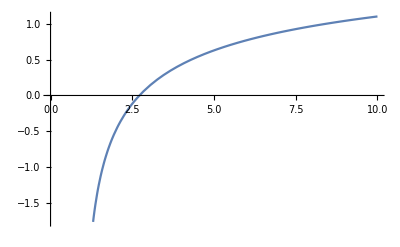

```mathematica
Q={p0, p1, q0, q1};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]]
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
Z=leadingSeries[Sqrt[(Q.Σ.ΠS[z])(Q.Σ.ΠSc[zc])]/Sqrt[-I ΠSc[zc].Σ.ΠS[z]],z,zc];

CargaZ2=(Q.Σ.ΠS[z])(Q.Σ.ΠSc[zc])/(-I ΠSc[zc].Σ.ΠS[z]);
leadingSeries[CargaZ2, z, zc]//Simplify;
Print["Carga central |Z|^2 a leading terms:"]
Print["|Z|^2= ", leadingSeries[CargaZ2, z, zc]//Simplify]
Print["Check |Z|^2= ", leadingSeries2[CargaZ2, z, zc]//FullSimplify]
Print["Leading terms check a z->0:"]
Print["Expresión completa |Z|^2= ",CargaZ2/.{z->0.00000000001,zc->0.00000000001,p0->p0,p1->p1,q0->q0,q1->q1}]
Print["Expresión lead terms |Z|^2 = ",leadingSeries[CargaZ2, z, zc]/.{z->0.00000000001,zc->0.00000000001,p0->p0,p1->p1,q0->q0,q1->q1}//Expand]
Print["--------------------------------------------------------------------------------"]
Atractor=Sum[Q[[i]]Σ[[i,j]]ΠMt[[j,l]]Σ[[k,l]]ΠSc[zc][[k]] ,{i,1,4},{j,1,4},{k,1,4},{l,1,4}]//Expand//Chop;
Print["Derivada de la carga central a leading terms: "]
Solucion=leadingSeries[Atractor, z, zc] ;
Print["∂|Z|= ", leadingSeries[Atractor, z, zc]]
Print["Leading terms check a z->0:"]
Print["Expresión completa ∂|Z|= ",Atractor/.{z->0.000000000001,zc->0.000000000001,p0->p0,p1->p1,q0->q0,q1->q1}//Expand] 
Print["Expresión lead terms ∂|Z|= ",leadingSeries[Atractor, z, zc]/.{z->0.000000000001,zc->0.000000000001,p0->p0,p1->p1,q0->q0,q1->q1}//Expand ]
```

# PRUEBA QUINTIC PAPER VAFA Polar

```mathematica
LCSLQ = (2 Pi I /5)^3 {{5/6 t^3+25/12 t},{-5/2 t^2-1/2 t},{1},{t}} /. {t-> 1/(2 Pi I)Log[z]};
MatrixForm[LCSLQ]
```

(-8/125 ⅈ π^3 (-(25 ⅈ Log[z])/(24 π)+(5 ⅈ Log[z]^3)/(48 π^3))
-8/125 ⅈ π^3 ((ⅈ Log[z])/(4 π)+(5 Log[z]^2)/(8 π^2))
-(8 ⅈ π^3)/125
-4/125 π^2 Log[z])

```mathematica
LCSLQSt = LCSLQ /. Log[z]-> 2 Pi I t
```

{{-8/125 ⅈ π^3 ((25 t)/12+(5 t^3)/6)},{-8/125 ⅈ π^3 (-t/2-(5 t^2)/2)},{-(8 ⅈ π^3)/125},{-8/125 ⅈ π^3 t}}

```mathematica
LCSLQS =(LCSLQ /. Log[z]-> 2 Pi I t)/.{t->-I Log[r]/(2 Pi)+ p/(2 Pi)}//Expand
```

{{-(ⅈ p^3)/150-1/15 ⅈ p π^2-1/50 p^2 Log[r]-1/15 π^2 Log[r]+1/50 ⅈ p Log[r]^2+Log[r]^3/150},{1/25 ⅈ p^2 π+2/125 ⅈ p π^2+2/25 p π Log[r]+2/125 π^2 Log[r]-1/25 ⅈ π Log[r]^2},{-(8 ⅈ π^3)/125},{-4/125 ⅈ p π^2-4/125 π^2 Log[r]}}

```mathematica
pitilde=-Table[D[LCSLQ[[j]],t]LCSLQ[[i]]-LCSLQ[[j]]D[LCSLQ[[i]],t],{i,1,4},{j,1,4}] ;
```

```mathematica
piconjug = {{(2 p π^3)/15-(4 p^3 π^3)/75+2/15 ⅈ π^3 Log[r]-4/25 ⅈ p^2 π^3 Log[r]+4/25 p π^3 Log[r]^2+4/75 ⅈ π^3 Log[r]^3},{-(4 p π^3)/125+4/25 ⅈ p^2 π^3-4/125 ⅈ π^3 Log[r]-8/25 p π^3 Log[r]-4/25 ⅈ π^3 Log[r]^2},{(8 ⅈ π^3)/125},{(8 p π^3)/125+8/125 ⅈ π^3 Log[r]}};
```

```mathematica
p0 = (n (2 Pi I / 5)^(-3) LCSLQS[[1]] +  n ( -2 Pi I / 5)^(-3) piconjug[[1]]) //Expand
p1 = (n (2 Pi I / 5)^(-3) LCSLQS[[2]] +  n ( -2 Pi I / 5)^(-3) piconjug[[2]]) //Expand
q0 = (n (2 Pi I / 5)^(-3) LCSLQS[[3]] +  n ( -2 Pi I / 5)^(-3) piconjug[[3]]) //Expand
q1 = (n (2 Pi I / 5)^(-3) LCSLQS[[4]] +  n ( -2 Pi I / 5)^(-3) piconjug[[4]]) //Expand
QU={p0,q0,p1,q1}
```

{25/6 n Log[r]-5 n p^2 Log[r]+5/3 n Log[r]^3}

{5 n p^2-n Log[r]-5 n Log[r]^2}

{2 n}

{2 n Log[r]}

{{25/6 n Log[r]-5 n p^2 Log[r]+5/3 n Log[r]^3},{2 n},{5 n p^2-n Log[r]-5 n Log[r]^2},{2 n Log[r]}}

```mathematica
Cargacentral=Transpose[QU].Σ.LCSLQS Transpose[QU].Σ.piconjug/(-I Transpose[piconjug].Σ.LCSLQS) //Simplify
```

{{1/(120 p (-5+8 p^2))n^2 (p (24-125 p^2+50 p^4)+(-74 ⅈ+37 p+245 ⅈ p^2-10 p^3-150 ⅈ p^4) Log[r]+(-37 ⅈ+245 p+30 ⅈ p^2-200 p^3) Log[r]^2+5 (-41 ⅈ+6 p+40 ⅈ p^2) Log[r]^3+10 (-ⅈ+15 p) Log[r]^4-50 ⅈ Log[r]^5) (p (24-125 p^2+50 p^4)+(74 ⅈ+37 p-245 ⅈ p^2-10 p^3+150 ⅈ p^4) Log[r]+(37 ⅈ+245 p-30 ⅈ p^2-200 p^3) Log[r]^2+5 (41 ⅈ+6 p-40 ⅈ p^2) Log[r]^3+10 (ⅈ+15 p) Log[r]^4+50 ⅈ Log[r]^5)}}

```mathematica
leadingSeries[Cargacentral,r,p]
```

{{-1/(600 p)n^2 (-74 ⅈ Log[r]-37 ⅈ Log[r]^2-205 ⅈ Log[r]^3-10 ⅈ Log[r]^4-50 ⅈ Log[r]^5) (74 ⅈ Log[r]+37 ⅈ Log[r]^2+205 ⅈ Log[r]^3+10 ⅈ Log[r]^4+50 ⅈ Log[r]^5)}}

```mathematica
Atractor=Sum[QU[[i]]Σ[[i,j]]pitilde[[j,l]]Σ[[k,l]]piconjug[[k]] ,{i,1,4},{j,1,4},{k,1,4},{l,1,4}]/.{r->0}//Expand//Simplify
```

Infinity::indet: Indeterminate expression -(4 p π^3)/125+4/25 ⅈ p^2 π^3+(-ⅈ) ∞+ⅈ ∞+p ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate}

# PRUEBA QUINTIC PAPER VAFA x+iy

```mathematica
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]]
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(*LCSLQ = (2 Pi I /5)^3 {1,t,5/6 t^3+25/12 t,-5/2 t^2-1/2 t};*)
LCSLQ = {ΠS[z][[3]], ΠS[z][[4]],ΠS[z][[1]]-(0.-0.9692044900729202 ⅈ),ΠS[z][[2]]-25/12}/.{Log[z]-> 2 Pi I t};
Print["Period vector with t=-5/(2  πⅈ)Log(5φ) :"]
MatrixForm[LCSLQ]
Print["----------------------------------------------------------------"]
LCSLQS =LCSLQ/.{t->x+I y}//Expand;
Print["Period vector with t→x+ⅈy :"]
MatrixForm[LCSLQS]
Print["----------------------------------------------------------------"]
pitilde=-Table[D[LCSLQ[[j]],t]LCSLQ[[i]]-LCSLQ[[j]]D[LCSLQ[[i]],t],{i,1,4},{j,1,4}] /. {t->x+I y};
piconjug =( Conjugate[LCSLQS]//ComplexExpand );
Print["Conjugate Period vector with t→x+ⅈy :"]
MatrixForm[piconjug]
Print["----------------------------------------------------------------"]
Print["Charges Q at Attractor Point :"]
p0 = (n (2 Pi I /5)^(-3) LCSLQS[[1]] +  n ( -2 Pi I/5)^(-3) piconjug[[1]]) // Simplify ;
p1 = (n (2 Pi I /5)^(-3) LCSLQS[[2]] +  n ( -2 Pi I /5)^(-3) piconjug[[2]]) //Simplify ;
q0 = (n (2 Pi I /5)^(-3) LCSLQS[[3]] +  n ( -2 Pi I /5)^(-3) piconjug[[3]]) //Simplify ; 
q1 = (n (2 Pi I /5)^(-3) LCSLQS[[4]] +  n ( -2 Pi I /5)^(-3) piconjug[[4]]) //Simplify ;
QU={p0,p1,q0,q1};
MatrixForm[QU]
Print["----------------------------------------------------------------"]
Print["Entropy / Central Charge, S = π |Z|^2 =", leadingSeries[Pi(QU.Σ.LCSLQS)(QU.Σ.piconjug)/(-I piconjug.Σ.LCSLQS),y,x]//Simplify // Expand ]
Print["----------------------------------------------------------------"]
sel=1;
If[sel≠1,
PIforKC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(LCSLQ[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
PIforKC[tc_]:=(Conjugate[LCSLQ]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}]
PIforKC[tc];
MatrixForm[PIforKC[tc]];
K[t_,tc_]:=-Log[-I PIforKC[tc].Σ.LCSLQ];
(* metrica de Kahler*)
Print["Metrica de Kahler"]
G[1,1]=D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
Print["g_(t,tc)= ", G[1,1]//Simplify//Expand]
Print["Metrica de Kahler leading terms"]
g = leadingSeries[G[1,1],t,tc]/.{t-> x+I y, tc-> x- I y}//Expand;
Print["g_(t,tc)= ",g/.x->0]
Print["--------------------------------------------------------------------------------"]
distance = Integrate[Sqrt[g/.x->0],y]//Simplify;
Print["d = ∫√(g_(z,zc))ⅆz = ", distance]
Print["--------------------------------------------------------------------------------"]
Solve[ d - distance == 0, y]
(*Print["t = ", T = leadingSeries[Series[1/(2 Pi I)wM1/wM0,{z,0,3}],z,zc] ]
Print["--------------------------------------------------------------------------------"]
Plot[d,{z,0,10}]*)
```

Period vector with t=-5/(2  πⅈ)Log(5φ) :

(1
t
(0.+0. ⅈ)+(25 t)/12+(265 t^3)/12
-(11 t)/2-(15 t^2)/2)

----------------------------------------------------------------

Period vector with t→x+ⅈy :

(1
x+ⅈ y
(0.+0. ⅈ)+(25 x)/12+(265 x^3)/12+(25 ⅈ y)/12+265/4 ⅈ x^2 y-(265 x y^2)/4-(265 ⅈ y^3)/12
-(11 x)/2-(15 x^2)/2-(11 ⅈ y)/2-15 ⅈ x y+(15 y^2)/2)

----------------------------------------------------------------

Conjugate Period vector with t→x+ⅈy :

(1
x-ⅈ y
0.+(25 x)/12+(265 x^3)/12-(265 x y^2)/4+ⅈ (0.-(25 y)/12-(265 x^2 y)/4+(265 y^3)/12)
-(11 x)/2-(15 x^2)/2+(15 y^2)/2+ⅈ ((11 y)/2+15 x y))

----------------------------------------------------------------

Charges Q at Attractor Point :

(0
-(125 n y)/(4 π^3)
(0.+0. ⅈ)+(625 n y (-5-159 x^2+53 y^2))/(48 π^3)
(125 n (11+30 x) y)/(8 π^3))

----------------------------------------------------------------

Entropy / Central Charge, S = π |Z|^2 =(390625 n^2 y)/(384 π^5)

----------------------------------------------------------------

Metrica de Kahler

g_(t,tc)= -0.00889996/((0.+0. ⅈ)+0.0943396 t+t^3-0.0943396 tc-0.339623 t^2 tc+0.339623 t tc^2-1. tc^3)^2-(0.250979 t^2)/((0.+0. ⅈ)+0.0943396 t+t^3-0.0943396 tc-0.339623 t^2 tc+0.339623 t tc^2-1. tc^3)^2-(0.339623 t^4)/((0.+0. ⅈ)+0.0943396 t+t^3-0.0943396 tc-0.339623 t^2 tc+0.339623 t tc^2-1. tc^3)^2+(1.35849 t^3 tc)/((0.+0. ⅈ)+0.0943396 t+t^3-0.0943396 tc-0.339623 t^2 tc+0.339623 t tc^2-1. tc^3)^2-(0.250979 tc^2)/((0.+0. ⅈ)+0.0943396 t+t^3-0.0943396 tc-0.339623 t^2 tc+0.339623 t tc^2-1. tc^3)^2-(9.11534 t^2 tc^2)/((0.+0. ⅈ)+0.0943396 t+t^3-0.0943396 tc-0.339623 t^2 tc+0.339623 t tc^2-1. tc^3)^2+(1.35849 t tc^3)/((0.+0. ⅈ)+0.0943396 t+t^3-0.0943396 tc-0.339623 t^2 tc+0.339623 t tc^2-1. tc^3)^2-(0.339623 tc^4)/((0.+0. ⅈ)+0.0943396 t+t^3-0.0943396 tc-0.339623 t^2 tc+0.339623 t tc^2-1. tc^3)^2

Metrica de Kahler leading terms

g_(t,tc)= 1/y^2

--------------------------------------------------------------------------------

d = ∫√(g_(z,zc))ⅆz = √(1/y^2) y Log[y]

--------------------------------------------------------------------------------

{{y→1}}

```mathematica
ReX0 = 2 n
ReX1 = 2 n x
l (2n+I ImX1)^3/(ReX0+I ImX0)^2== 5/6 n x (5+2 x^2-6 y^2)
-3l (2n x+I ImX1)^2/(ReX0+I ImX0)== -n (x+5 x^2-5 y^2)
```

2 n

2 n x

(l (ⅈ ImX1+2 n)^3)/(ⅈ ImX0+2 n)^2==5/6 n x (5+2 x^2-6 y^2)

-(3 l (ⅈ ImX1+2 n x)^2)/(ⅈ ImX0+2 n)==-n (x+5 x^2-5 y^2)

```mathematica
Solve[{(l (I ImX1+2 n)^3)/(I ImX0+2 n)^2==5/6 n x (5+2 x^2-6 y^2),-(3 l (I ImX1+2 n x)^2)/(I ImX0+2 n)==-n (x+5 x^2-5 y^2)},{ImX1,ImX0},Reals]
```

```mathematica
(*Definir las ecuaciones complejas,asumiendo que ImX1 y ImX0 son reales*)eqns={(l (I ImX1+2 n)^3)/(I ImX0+2 n)^2==5/6 n x (5+2 x^2-6 y^2),-((3 l (I ImX1+2 n x)^2)/(I ImX0+2 n))==-n (x+5 x^2-5 y^2)};

(*Imponer que ImX1 y ImX0 sean reales*)
assumptions={ImX1∈Reals,ImX0∈Reals};

(*Resolver para ImX1 y ImX0 con las suposiciones*)
sol=Solve[eqns,{ImX1,ImX0},Complexes,Assumptions->assumptions];

(*Mostrar soluciones*)
sol
```

$Aborted

sol

# PRUEBA

```mathematica
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]]
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
LCSLQ = (2 Pi I /5)^3 {1,t,5/6 t^3+25/12 t,-5/2 t^2-1/2 t};
Print["Period vector with t=-5/(2  πⅈ)Log(5φ) :"]
MatrixForm[LCSLQ]
Print["----------------------------------------------------------------"]
LCSLQS =LCSLQ/.{t->x+I y}//Expand;
Print["Period vector with t→x+ⅈy :"]
MatrixForm[LCSLQS]
Print["----------------------------------------------------------------"]
pitilde=-Table[D[LCSLQ[[j]],t]LCSLQ[[i]]-LCSLQ[[j]]D[LCSLQ[[i]],t],{i,1,4},{j,1,4}] /. {t->x+I y};
piconjug =( Conjugate[LCSLQS]//ComplexExpand );
Print["Conjugate Period vector with t→x+ⅈy :"]
MatrixForm[piconjug]
Print["----------------------------------------------------------------"]
Print["Charges Q at Attractor Point :"]
p0 = (n (2 Pi I /5)^(-3) LCSLQS[[1]] +  n ( -2 Pi I/5)^(-3) piconjug[[1]]) // Simplify ;
p1 = (n (2 Pi I /5)^(-3) LCSLQS[[2]] +  n ( -2 Pi I /5)^(-3) piconjug[[2]]) //Simplify ;
q0 = (n (2 Pi I /5)^(-3) LCSLQS[[3]] +  n ( -2 Pi I /5)^(-3) piconjug[[3]]) //Simplify ; 
q1 = (n (2 Pi I /5)^(-3) LCSLQS[[4]] +  n ( -2 Pi I /5)^(-3) piconjug[[4]]) //Simplify ;
QU={p0,p1,q0,q1};
MatrixForm[QU]
Print["----------------------------------------------------------------"]
Print["Entropy / Central Charge, S = π |Z|^2 =", Pi(QU.Σ.LCSLQS)(QU.Σ.piconjug)/(-I piconjug.Σ.LCSLQS)//Simplify // Expand ]
```

Period vector with t=-5/(2  πⅈ)Log(5φ) :

(-(8 ⅈ π^3)/125
-8/125 ⅈ π^3 t
-8/125 ⅈ π^3 ((25 t)/12+(5 t^3)/6)
-8/125 ⅈ π^3 (-t/2-(5 t^2)/2))

----------------------------------------------------------------

Period vector with t→x+ⅈy :

(-(8 ⅈ π^3)/125
-8/125 ⅈ π^3 x+(8 π^3 y)/125
-2/15 ⅈ π^3 x-4/75 ⅈ π^3 x^3+(2 π^3 y)/15+4/25 π^3 x^2 y+4/25 ⅈ π^3 x y^2-(4 π^3 y^3)/75
4/125 ⅈ π^3 x+4/25 ⅈ π^3 x^2-(4 π^3 y)/125-8/25 π^3 x y-4/25 ⅈ π^3 y^2)

----------------------------------------------------------------

Conjugate Period vector with t→x+ⅈy :

((8 ⅈ π^3)/125
8/125 ⅈ π^3 x+(8 π^3 y)/125
(2 π^3 y)/15+4/25 π^3 x^2 y-(4 π^3 y^3)/75+ⅈ ((2 π^3 x)/15+(4 π^3 x^3)/75-4/25 π^3 x y^2)
-(4 π^3 y)/125-8/25 π^3 x y+ⅈ (-(4 π^3 x)/125-(4 π^3 x^2)/25+(4 π^3 y^2)/25))

----------------------------------------------------------------

Charges Q at Attractor Point :

(2 n
2 n x
5/6 n x (5+2 x^2-6 y^2)
-n (x+5 x^2-5 y^2))

----------------------------------------------------------------

Entropy / Central Charge, S = π |Z|^2 =25/6 n^2 π y-20/3 n^2 π y^3

```mathematica
pi = ΠS[z]/. Log[z]-> 2 I Pi t
```

{(0.-0.969204 ⅈ)+(25 t)/12+(265 t^3)/12,25/12-(11 t)/2-(15 t^2)/2,1,t}

```mathematica
piR = pi /. {t->-I Log[r]/(2 Pi)+ p/(2 Pi)}//Expand
```

{(0.-0.969204 ⅈ)+(265 p^3)/(96 π^3)+(25 p)/(24 π)-(265 ⅈ p^2 Log[r])/(32 π^3)-(25 ⅈ Log[r])/(24 π)-(265 p Log[r]^2)/(32 π^3)+(265 ⅈ Log[r]^3)/(96 π^3),25/12-(15 p^2)/(8 π^2)-(11 p)/(4 π)+(15 ⅈ p Log[r])/(4 π^2)+(11 ⅈ Log[r])/(4 π)+(15 Log[r]^2)/(8 π^2),1,p/(2 π)-(ⅈ Log[r])/(2 π)}

```mathematica
pitilde2=-Table[D[pi[[j]],t]pi[[i]]-pi[[j]]D[pi[[i]],t],{i,1,4},{j,1,4}];
```

```mathematica
conjug =( Conjugate[piR]//ComplexExpand )/. {Arg[r]-> 0, Log[r^2]-> 2Log[r]}
```

{0.+(265 p^3)/(96 π^3)+(25 p)/(24 π)-(265 p Log[r]^2)/(32 π^3)+ⅈ (0.969204+(265 p^2 Log[r])/(32 π^3)+(25 Log[r])/(24 π)-(265 Log[r]^3)/(96 π^3)),25/12-(15 p^2)/(8 π^2)-(11 p)/(4 π)+(15 Log[r]^2)/(8 π^2)+ⅈ (-(15 p Log[r])/(4 π^2)-(11 Log[r])/(4 π)),1,p/(2 π)+(ⅈ Log[r])/(2 π)}

```mathematica
picon ={(0.+0.9692044900729202 ⅈ)+(265 p^3)/(96 π^3)+(25 p)/(24 π)+(265 ⅈ p^2 Log[r])/(32 π^3)+(25 ⅈ Log[r])/(24 π)-(265 p Log[r]^2)/(32 π^3)-(265 ⅈ Log[r]^3)/(96 π^3),25/12-(15 p^2)/(8 π^2)-(11 p)/(4 π)-(15 ⅈ p Log[r])/(4 π^2)-(11 ⅈ Log[r])/(4 π)+(15 Log[r]^2)/(8 π^2),1,p/(2 π)+(ⅈ Log[r])/(2 π)}
```

{(0.+0.969204 ⅈ)+(265 p^3)/(96 π^3)+(25 p)/(24 π)+(265 ⅈ p^2 Log[r])/(32 π^3)+(25 ⅈ Log[r])/(24 π)-(265 p Log[r]^2)/(32 π^3)-(265 ⅈ Log[r]^3)/(96 π^3),25/12-(15 p^2)/(8 π^2)-(11 p)/(4 π)-(15 ⅈ p Log[r])/(4 π^2)-(11 ⅈ Log[r])/(4 π)+(15 Log[r]^2)/(8 π^2),1,p/(2 π)+(ⅈ Log[r])/(2 π)}

```mathematica
p0 = (n (2 Pi I / 5)^(-3) piR[[1]] +  n ( -2 Pi I / 5)^(-3) conjug[[1]]) //Expand
p1 = (n (2 Pi I / 5)^(-3) piR[[2]] +  n ( -2 Pi I / 5)^(-3) conjug[[2]]) //Expand
q0 = (n (2 Pi I / 5)^(-3) piR[[3]] +  n ( -2 Pi I / 5)^(-3) conjug[[3]]) //Expand
q1 = (n (2 Pi I / 5)^(-3) piR[[4]] +  n ( -2 Pi I / 5)^(-3) conjug[[4]]) //Expand
QU={leadingSeries[p0,r,p],leadingSeries[p1,r,p],leadingSeries[q0,r,p],leadingSeries[q1,r,p]}
```

(0.976823+0. ⅈ) n+(33125 n p^2 Log[r])/(128 π^6)+(3125 n Log[r])/(96 π^4)-(33125 n Log[r]^3)/(384 π^6)

-(1875 n p Log[r])/(16 π^5)-(1375 n Log[r])/(16 π^4)

0

(125 n Log[r])/(8 π^4)

{(0.976823+0. ⅈ) n+(3125 n Log[r])/(96 π^4)-(33125 n Log[r]^3)/(384 π^6),-(1375 n Log[r])/(16 π^4),0,(125 n Log[r])/(8 π^4)}

```mathematica
Cargacentral=Transpose[QU].Σ.piR Transpose[QU].Σ.picon/(-I Transpose[picon].Σ.piR) //Simplify
```

((0.0560711+0. ⅈ) n^2)/((0.196392+0. ⅈ)-(1.+0. ⅈ) x^3+(1.98592+0. ⅈ) x y^2)

```mathematica
leadingSeries[Cargacentral,y,x]
```

(0.285505+0. ⅈ) n^2

```mathematica
Atractor=Sum[QU[[i]]Σ[[i,j]]pitilde2[[j,l]]Σ[[k,l]]picon[[k]] ,{i,1,4},{j,1,4},{k,1,4},{l,1,4}]/.{x->0}//Expand//Simplify
```

n ((0.+3.63163 ⅈ) ⅇ^(2 ⅈ p) r^2+0.822255 ⅇ^(ⅈ p) r y-(0.+0.411128 ⅈ) y^2)

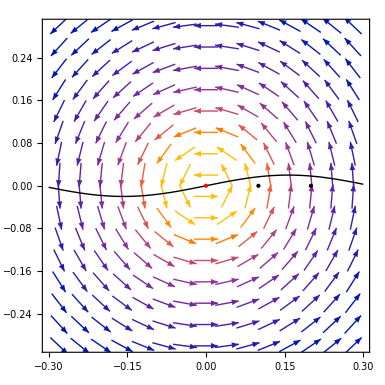

```mathematica
(*Definir el campo vectorial,por ejemplo,un campo de vórtice*)vectorField[x_,y_]:={-y/(x^2+y^2),x/(x^2+y^2)}

(*Gráfico del campo vectorial*)
vectorPlot=VectorPlot[vectorField[x,y],{x,-0.3,0.3},{y,-0.3,0.3},VectorStyle->Arrowheads[Small],VectorScale->Small];

(*Línea ondulante,por ejemplo,una función senoidal*)
wavyLine=Plot[Sin[10 x]/50,{x,-0.3,0.3},PlotStyle->{Black,Thick},Exclusions->None];

(*Puntos o singularidades*)
singularities=Graphics[{Red,PointSize[Large],Point[{0,0}],Black,PointSize[Medium],Point[{0.1,0}],Point[{0.2,0}]}];

(*Combinar todos los elementos*)
Show[vectorPlot,wavyLine,singularities]
```

```mathematica
Transpose[Q].Σ.ΠStxy //Simplify
```

n ((0.+0.969204 ⅈ)-10.8333 x^3-(0.+32.5 ⅈ) x^2 y+40. x y^2+(0.+18.3333 ⅈ) y^3)

Qcharges

```mathematica
k
```

-1. (3.91202+Log[0.0387682-1. x^2 y+0.733333 y^3])

```mathematica
Series[S,{y,Infinity,1}]/Series[Z,{y,Infinity,1}]/.{x->0}
```

(0.-9.51164 ⅈ) n y^(3/2)+(0.-2.22045×10^-16 ⅈ) n √(1/y)+O[1/y]^(3/2)

```mathematica
2 Exp[k/2]Series[S,{y,Infinity,1}]/Series[Z,{y,Infinity,1}]/.{x->0} //Normal //Expand
```

-((0.+3.14159 ⅈ) n y^(3/2))/((y^3)^0.5)

-((0.+3.14159 ⅈ) n y^(3/2))/((y^3)^0.5)

```mathematica
Series[Exp[ Log[ - I ΠSc[zc].Σ.ΠS[z]]],{z,0,1}]
```

-0.043674 (-44.3836-1.61833×10^-15 Log[z]+1. Log[z]^3-1.61833×10^-15 Log[zc]+0.692308 Log[z]^2 Log[zc]+0.692308 Log[z] Log[zc]^2+1. Log[zc]^3)+O[z]^2

```mathematica
(*Definir la parametrización de la worldsheet*)Clear[x,t]
(*Parámetros de la cuerda:amplitud y número de ondas*)
A=0.2; (*Amplitud reducida para menos oscilación*)
k=Pi; (*Número de ondas reducido para menos ciclos*)
ω=Pi; (*Frecuencia angular reducida*)

(*Ecuación de la cuerda oscilante en función del espacio y el tiempo*)
x[t_,sigma_]:=A Sin[k sigma-ω t];

(*Generar la worldsheet:parametrización en función de tiempo t y la posición a lo largo de la cuerda sigma*)
worldsheet=ParametricPlot3D[{sigma,t,x[t,sigma]},{sigma,0,2},{t,0,2},Mesh->None,PlotStyle->Opacity[0.7,Blue],AxesLabel->{"Sigma (posición)","Tiempo","X(t, sigma) (desplazamiento)"},Boxed->False,PlotRange->All,ImageSize->Large];

(*Mostrar la worldsheet*)
worldsheet
```

-Graphics3D-

```mathematica
(*PRIMER PERIODO*)
Num = 3; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
(*PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 5(5z D[#,z]+1 #)&[(5z D[#,z]+2#)&[(5z D[#,z]+3#)&[(5z D[#,z]+4#)&[F]]]]*)
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
tri = PF[z, AnsaM[z, x, Num]] // Expand ; (* Aplicar el operador en el Ansatz*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}](* Tomamos los coeficientes de las potencias de z*)
f[0]=1;
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];(* Resolvemos para el Ansatz dado*)
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
Take[solM[0],sample]; (*Soluciones *)
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
(*Print["1st Period Π_1(...)= ",wM0]*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía *)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
Take[TotM,sample]; (*L (w0M Log[z]+w1M)= *)
Take[Coefficient[TotM,z,xb],sample]; (*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)
Coefficient[TotM,z,0]; (*El coeficiente z^0 en L (w0M Log[z]+w1M) es *)
var2=Table[b[k],{k,0,Num}];
Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}]; (*Ecuaciones :*)
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
Take[solbM,sample]; (*Soluciones *)
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand; (*<-----------BASE*)
(*Print["2st Period Π_2(...)= ",wM1];*)
(*TERCER PERIODO*)
(*Nuevo ansatz 1/2 wM0 Log[z]^2+w1M Log[z]+w2M "];*)
Take[1/2 Log[z]^2*w0[z]+ Log[z]w1[z]//Expand,sample];(*<-----------BASE*)
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
Take[AnsaC[z,xc,Num]//Expand,sample]//Factor; (*w2M= *)
Clear[Tot2];
Tot2=PF[z,1/2 Log[z]^2*w0[z]+Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];(*<-----------BASE*)
Take[Tot2//Expand,sample]//Expand; (*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)
Take[PF[z,1/2 Log[z]^2*w0[z]+ Log[z]w1[z]]//Expand,sample]; (*L(wM0 Log[z]^2+2 Log[z] wM1)=*)(*<-----------BASE*)
Coefficient[Tot2,z,xc]/.{z->0}; (*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)
Coefficient[Tot2/.{xc->1},z,1]; (*Eval. xc->1  Coef. z^1 *)
Coefficient[Tot2/.{xc->1},z,2]; (*Eval. xc->1  Coef. z^2 *)
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
Take[w2[z]//Expand,sample]; (*w2 = *)
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}]; (*Ecuaciones *)
Take[solc,sample]; (*Soluciones*)
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=1/2 Log[z]^2*w0[z]+Log[z]w1[z]+w2[z] ;
wM2=  (1/2 Log[z]^2 wM0+ Log[z]w1[z]+w2[z])//Expand ; (*<-----------BASE*)
(* Print["3dt Period Π_3(...)= ", wM2] ; *)
(*CUARTO PERIODO*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
Clear[Tot3];
Tot3=PF[z, 1/6 Log[z]^3*w0[z]+1/2 Log[z]^2w1[z]+ Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;(*<-----------BASE*)
var2=Table[e[k],{k,0,Num}];
Take[Coefficient[Tot3,z,xd],sample]; (*Coeficiente z^xd(...) en L (Ansatz) *)
Coefficient[Tot3/.{xd->1},z,1]; (*Coeficiente z(...) en L (Ansatz)*)
Coefficient[Tot3/.{xd->1},z,2]; (*Coeficiente z^2(...) en L (Ansatz) *)
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
(*SMum[z_,3,Num]:=1/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
Take[5/6w3[z]//Expand,sample]; (*wM3= *)*)
wM3=  (1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 w1[z] + Log[z]w2[z] +  w3[z] )// Expand; (*<-----------BASE*)
(**)

leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
Π= {leadingSeries[wM0,z,zc],leadingSeries[wM1,z,zc],leadingSeries[wM2,z,zc],leadingSeries[wM3,z,zc]};

sigma = 1;
riemann = N[Zeta[3]];
(*Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),Mod[k/2,1]/(2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };*)
Msym ={{(riemann*χ)/((2π I)^3), c2D/(24 2 Pi I), 0, k/((2 Pi I)^3)}, {c2D/(24),-Mod[k,2]/(2 2 Pi I), -k/((2 Pi I)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 Pi I) , 0, 0} };
(*Quintic vacua Msym ={{(riemann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, 1/((2π ⅈ)^3)}, {c2D/(24),-11/(2 2 π ⅈ), -1/((2π ⅈ)^2), 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };*)
(*Print["Matriz de transición a base simpléctica:"]
Print["M_M,S="MatrixForm[Msym]]*)

(* periodos en la base simplectica*)
ΠS[z_]:= Msym.Π;
ΠS[z]//Expand;
(*Print["Periodos en base Simpléctica:"]
Print["ΠS=", MatrixForm[ΠS[z]]//Expand]*)

(* periodos conjugados en la base simplectica*)
sel=1;
If[sel≠1,
ΠSc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠS[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
ΠSc[zc_]:=(Conjugate[ΠS[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}]
ΠSc[zc];
(*Print["Periodos conjugados en base Simpléctica:"]
Print["ΠSc=", MatrixForm[ΠSc[zc]]//Expand];*)
(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
(* Matriz Pi tilde en el paper*)
ΠMt=-Table[D[ΠS[z][[j]],z]ΠS[z][[i]]-ΠS[z][[j]]D[ΠS[z][[i]],z],{i,1,4},{j,1,4}];
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]

ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
MatrixForm[ΠSt];


ΠSt = ΠS[z]/.{Log[z]-> 2 Pi I t};
(*ΠSt = (2 Pi I/5)^3{(0.-0.6202908736466689 ⅈ)+(8 t)/3+(104 t^3)/3,8/3+t/2-24 t^2,1,t};*)
ΠStxy = ΠSt/.{t->x+I y};

MatrixForm[ΠSt];
MatrixForm[ΠStxy];

ΠStxyC = Conjugate[ΠStxy]//ComplexExpand;

MatrixForm[ΠStxyC];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};
sel=1;
If[sel≠1,
ΠStC[tc_]:=Expand[Table[Plus@@(Conjugate[List@@(ΠSt[[k]]//Expand)]/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[tc]]-> tc Log[tc]}),{k,1,4}]],
ΠStC[tc_]:=(Conjugate[ΠSt]//Expand)/.{Conjugate[t]->tc, Conjugate[Log[t]]-> Log[tc],
Conjugate[t Log[t]]-> tc Log[tc]}];
ΠStC[tc];
MatrixForm[ΠStC[tc]];

q0 = (n  ΠStxy[[3]] +  n  ΠStxyC[[3]])//Simplify ; 
q1 = (n  ΠStxy[[4]] +  n  ΠStxyC[[4]]) //Simplify ;
p0 = (n  ΠStxy[[1]] +  n  ΠStxyC[[1]]) // Simplify ;
p1 = (n  ΠStxy[[2]] +  n  ΠStxyC[[2]]) //Simplify ;
QU=1/2 {p0=Select[Plus@@Expand[p0],Not[FreeQ[#,y]]&],Select[Plus@@Expand[p1],Not[FreeQ[#,y]]&],q0,q1};
Q = 1/2{p0/.{x->0},p1/.{x->0},q0/.{x->0},q1/.{x->0}};
Cargas = 1/2 {Series[p0,{y,Infinity,2}],Series[p1,{y,Infinity,2}],Series[q0,{y,Infinity,2}],Series[q1,{y,Infinity,2}]};
Gcargas = {P0,P1,Q0,Q1};
Qin = {0,n,-n y^2,0};
leadingSeries[expr_, z_,zc_] := Normal[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)} /. a_List :> Take[a, 1]];
lds[ex_,x_]:=( (ex/.x->(x+O[x]^2))/.SeriesData[U_,Z_,L_List,Mi_,Ma_,De_]:>SeriesData[U,Z,{L[[1]]},Mi,Mi+1,De]//Quiet//Normal);
K[t_,tc_]:=-Log[-I ΠStC[tc].Σ.ΠSt]
k=K[t,tc]/.{t->x+I y, tc->x-I y}//Simplify;
(* metrica de Kahler*)

G[1,1]=2 D[K[t,tc],t,tc];
(*leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
leadingSeries2[G[1,1], z, zc]//Simplify
metric=leadingSeries2[G[1,1], z, zc]/.zc->z//Simplify;
gzzc = Series[metric/. Log[z]->x /. z->Exp[x] , {x,Infinity, 3}]/. x->Log[z] //Simplify //Normal;*)
g = G[1,1]/.{t-> x+I y, tc-> x-I y}//Simplify ;
glead = Series[g,{y,Infinity,3}]//Simplify;
distance = Integrate[Sqrt[glead/.x->0],y];

Sol = Solve[distance==d, y];

Z = QU.Σ.ΠStxy/(Sqrt[-I ΠStxyC.Σ.ΠStxy])//Simplify;
Sent = Pi (QU.Σ.ΠStxy)(QU.Σ.ΠStxyC)/(-I ΠStxyC.Σ.ΠStxy)//Simplify;
S = Series[Sent,{y,Infinity,1}] //Simplify;
 S/.{x->0}
TeXForm[ S/.{x->0}]
```

16.7552 n^2 y^3-8.37758 n^2 y+0.974351 n^2+(1.0472 n^2)/y+O[1/y]^2

16.7552 n^2 y^3-8.37758 n^2 y+0.974351 n^2+\frac{1.0472 n^2}{y}+O\left(\left(\frac{1}{y}\right)^2\right)

```mathematica
data={5.235987755982989,1.0471975511965976,16.755160819145562,9.42477796076938,12.566370614359172,8.377580409572781,2.0943951023931953,3.141592653589793,1.0471975511965976,4.1887902047863905,6.283185307179586,2.0943951023931953,1.0471975511965976,4.1887902047863905,-1};
dataORD=Sort[data]
elements={"CY1","CY2","CY3","CY4","CY5","CY6","CY7","CY8","CY9","CY10","CY11","CY12","CY13","CY14"};

elementsX = {"X_5(1^5)", "X_10(1^32^15^1)", "X_(2, 2, 2, 2)(1^8)", "X_(3, 3)(1^6)", "X_(3, 2, 2)(1^7)", "X_(4, 2)(1^6)", "X_8(1^44^1)", "X_6(1^42^1)", "X_(12, 2)(1^44^16^1)", "X_(4, 4)(1^42^2)", "X_(4, 3)(1^52^1)",
   "X_(6, 4)(1^32^23^1)", "X_(6, 6)(1^22^23^2)", "X_(6, 2)(1^53^1)",""};

elementsXORD = {"","X_(6, 6)(1^22^23^2)","X_(12, 2)(1^44^16^1)","X_10(1^32^15^1)","X_(6, 4)(1^32^23^1)","X_8(1^44^1)","X_6(1^42^1)","X_(6, 2)(1^53^1)","X_(4, 4)(1^42^2)","X_5(1^5)","X_(4, 3)(1^52^1)","X_(4, 2)(1^6)","X_(3, 3)(1^6)","X_(3, 2, 2)(1^7)","X_(2, 2, 2, 2)(1^8)"}


(*Aumentar el espaciado entre los puntos en el eje X*)
xPositions=Range[1,Length[data],0.5];

dataPlot=ListPlot[data,PlotStyle->PointSize[Large],PlotStyle->Red,AxesOrigin->{0,18},Axes->{None,True},PlotRange->{Automatic,{0,18}}];
labels=MapThread[Text[#1,{#2,#3+0.5}]&,{elementsX,xPositions,data}];
Show[dataPlot,Graphics[labels]]

dataPlotORD=ListPlot[dataORD,PlotStyle->PointSize[Large],PlotStyle->Red,AxesOrigin->{0,18},Axes->{None,True},PlotRange->{Automatic,{0,18}}];
labelsORD=MapThread[Text[#1,{#2,#3+0.5}]&,{elementsXORD,xPositions,dataORD}];
Show[dataPlotORD,Graphics[labelsORD]]
```

{-1,1.0472,1.0472,1.0472,2.0944,2.0944,3.14159,4.18879,4.18879,5.23599,6.28319,8.37758,9.42478,12.5664,16.7552}

{,X_(6, 6)(1^22^23^2),X_(12, 2)(1^44^16^1),X_10(1^32^15^1),X_(6, 4)(1^32^23^1),X_8(1^44^1),X_6(1^42^1),X_(6, 2)(1^53^1),X_(4, 4)(1^42^2),X_5(1^5),X_(4, 3)(1^52^1),X_(4, 2)(1^6),X_(3, 3)(1^6),X_(3, 2, 2)(1^7),X_(2, 2, 2, 2)(1^8)}

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Text[#1,{#2,#3+0.5}]&,{{X_5(1^5),X_10(1^32^15^1),X_(2, 2, 2, 2)(1^8),«6»,X_(4, 4)(1^42^2),«5»},{«1»},{5.23599,1.0472,16.7552,«6»,4.18879,«5»}}]; dimensions are 15 and 29.

-Graphics-

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Text[#1,{#2,#3+0.5}]&,{{,X_(6, 6)(1^22^23^2),X_(12, 2)(1^44^16^1),«5»,X_(4, 4)(1^42^2),X_5(1^5),«5»},{1.,«9»,«19»},{-1,«9»,«5»}}]; dimensions are 15 and 29.

-Graphics-